# Beyond typology beyond optimization Part 1

## b) Quantitative Evaluation, c) HSO and Self Organizing Maps

The code is structured as follows:
Cells in yellow are variables that need to be check, always run first 
Cells in red contain code to load data, always after the yellow cells
Cells in blue contain code, always run in order
Cells in white are to check the consistency of the data, not need to run

## Functions

```mathematica
IDcreate [somX_,somY_,somD_]:=
Block[{somCoords,somLen,somWeights,distances},
somCoords=Flatten[Table[{i,j},{i,1.,somX},{j,1.,somY}],1];
somLen=somX * somY;
somWeights=RandomReal[1,{somLen, somD}];
somWeights=Normalize@#&/@somWeights;
distances=N[Sqrt[DistanceMatrix[somCoords,DistanceFunction->SquaredEuclideanDistance]]];
<|
"dimensions"-> <|"x"-> somX,"y"-> somY,"dim"-> somD, "len"-> somX*somY|>,
"weights"-> somWeights, 
"coordinates"->somCoords,
"distances"->distances
|>
]
```

```mathematica
IDimage[som_]:=
Image[Partition[Transpose[Transpose[som["weights"]][[1;;3]]],som["dimensions","y"]]]

IDslices[som_,method_]:=
ArrayPlot[Partition[#, som["dimensions","y"]], ColorFunction->ColorData[method]]&/@ Transpose[som["weights"]]
```

```mathematica
IDtrain[som_,vec_,sel_,ite_]:=
Block[{weights,distances,dim,somLen,sig,inputN,bmus,ns,allNS,nst},
weights = som["weights"];
distances = som["distances"];
dim = som["dimensions"][[1;;2]];
somLen = som["dimensions","len"];

For[u=0,u<=ite,u++,
sig = N[Nest[(1-(u/(ite+1)))*#&,Max[dim]/2,1]];
inputN = RandomSample[vec, sel];
bmus = First/@Nearest[MapIndexed[#1->#2[[1]]&,weights],inputN];
ns = Exp[-(distances[[#]])^2 /(2 sig^2)]&/@ bmus;
allNS = Total@ns;
nst = Transpose@ns;
weights = Total[inputN*nst[[#]]]/allNS[[#]]&/@ Range[1, somLen];Print@u;
];

weights
]
```

```mathematica
IDask[som_,vec_]:=
First/@Nearest[MapIndexed[#1->#2[[1]]&,som["weights"]],vec]

IDerror[som_,vec_]:=
Block[{bmus},
bmus=IDask[som, vec];
Mean@ParallelTable[EuclideanDistance[vec[[h]],som["weights"][[bmus[[h]]]]],{h,1,vec//Length}]
]
```

```mathematica
EuclideanDistanceIncomplete[v1_,v2_]:= 
EuclideanDistance@@Transpose[Select[Transpose[{v1,v2}],NumberQ@#[[1]]&]]

IDaskIncomplete[som_,vec_]:=
Flatten@Nearest[MapIndexed[#1->#2[[1]]&,som["weights"]],vec, DistanceFunction->EuclideanDistanceIncomplete]
```

```mathematica
ImportEdgeConnection[edgeNode_]:=
Block[{edgesConection},
edgesConection=Import[NotebookDirectory[]<>edgeNode];
edgesConection=1+#&/@#&/@edgesConection;
Return@edgesConection
]
```

```mathematica
CheckEdge[force_,edge_,thres_]:=!MemberQ[(force[[#]]>0&&edge[[#]]≥ thres)&/@Range@Length@force,True];
```

```mathematica
FilterLenght[subset_,thres_]:=
Block[
{keepOrNot,keepInput,keepPoints,keepEdges,keepForce},

keepOrNot=CheckEdge[subset["force"][[#]],subset["edges"][[#]],thres]&/@Range@Length@subset["force"];

keepInput=Pick[subset["input"],keepOrNot,True];
keepEdges=Pick[subset["edges"],keepOrNot,True];
keepForce=Pick[subset["force"],keepOrNot,True];
keepPoints=Pick[subset["points"],keepOrNot,True];

<|
"input"->keepInput,
"points"->keepPoints,
"edges"->keepEdges,
"force"->keepForce

|>
]
```

```mathematica
CheckRadius[radius_,thres_]:=!MemberQ[(# ≥ thres)&/@radius,True];
```

```mathematica
FilterArea[subset_,radius_,thres_]:=
Block[
{keepOrNot,keepInput,keepiPoints,keepEdges,keepForce,keepRadius},

keepOrNot=CheckRadius[#,thres]&/@radius;

keepInput=Pick[subset["input"],keepOrNot,True];
keepEdges=Pick[subset["edges"],keepOrNot,True];
keepForce=Pick[subset["force"],keepOrNot,True];
keepiPoints=Pick[subset["points"],keepOrNot,True];
keepRadius=Pick[radius,keepOrNot,True];

<|
"input"->keepInput,
"edges"->keepEdges,
"force"->keepForce,
"points"->keepiPoints,
"radius"-> keepRadius
|>
]
```

```mathematica
CheckInertia[inertia_,thres_]:=!MemberQ[(# ≥ thres)&/@inertia,True];
```

```mathematica
FilterSlenderness[subsetMaxArea_,inertia_,thres_]:=
Block[
{keepOrNot,keepInput,keepiPoints,keepEdges,keepForce},


keepOrNot=CheckInertia[#,thres]&/@inertia;

keepInput=Pick[subsetMaxArea[[1]],keepOrNot,True];
keepEdges=Pick[subsetMaxArea[[3]],keepOrNot,True];
keepForce=Pick[subsetMaxArea[[2]],keepOrNot,True];
keepiPoints=Pick[subsetMaxArea[[4]],keepOrNot,True];

<|
"input"->keepInput,
"edges"->keepEdges,
"force"->keepForce,
"points"->keepiPoints
|>
]
```

```mathematica
FilterLoadPath[subset_,percentage_]:=
Block[{input,points,edges,force,loadPath,sumloadPath,threshold,filter,inputFilter,filterPos,pos,pointsFilter,edgesFilter,forceFilter,loadPathFilter,absoluteEdges,absoluteForce,absoluteLoadPath},

input=subset["input"];
points=subset["points"];
edges=subset["edges"];
force=subset["force"];
loadPath=Times[edges,force];

absoluteEdges=Abs[#]&/@edges;
absoluteForce=Abs[#]&/@force;
absoluteLoadPath=Times[absoluteEdges,absoluteForce];
sumloadPath=Total[#]&/@absoluteLoadPath;

threshold=Floor@N[(Length[sumloadPath]*percentage)/100];
threshold=sumloadPath[[threshold]];

filter[x_]:=If[x>threshold,0,1];
filterPos=filter[#]&/@sumloadPath;

pos=Position[filterPos,0];

inputFilter=Delete[input,pos];
pointsFilter=Delete[points,pos];
edgesFilter=Delete[edges,pos];
forceFilter=Delete[force,pos];
loadPathFilter=Delete[loadPath,pos];

<|
"input"-> inputFilter,
"points"-> pointsFilter,
"edges"-> edgesFilter,
"force"-> forceFilter,
"loadPath"-> loadPathFilter
|>

]
```

```mathematica
HierOrderStatitics[vector_]:=
Block[{skns,mean,variance,kurtosis,stDeviation},
skns=Skewness[#]&/@vector;
mean=Mean[#]&/@vector;
variance=Variance[#]&/@vector;
kurtosis=Kurtosis[#]&/@vector;
stDeviation=StandardDeviation[#]&/@vector;
<|
"skns"-> skns,
"mean"-> mean,
"variance"-> variance,
"kurtosis"-> kurtosis,
"stDeviation"->stDeviation
|>
]
```

```mathematica
GetSom[bmus_,id_,vecListFilter_,method_]:=
Block[{table,allDims,color,somImg,indexListSorted,showList,lastDist,dist},


table =Table[id[[2]][[i,#]],{i,id[[2]]//Length}]&/@Range[id[[1,3]]];

allDims =Rescale[Re@Total@table];(*merge by channel / dimension / the total of eachh cell*)
color = ColorData[method][#]&/@allDims;(*getting the colors from the weights*)
somImg=Image[ArrayReshape[color, {id[[1,1]],id[[1,2]]}],ImageSize->Medium,ColorSpace->"RGB"];

indexListSorted=Function[{n},Keys@Select[bmus, #[[2]]==n&]]/@ Range@id[[1,4]];
showList=Table[-1,id[[1,4]]];

For[i=1,i≤id[[1,4]],i++,
lastDist=Infinity;
For[j=1,j≤Length@indexListSorted[[i]],j++,
dist=EuclideanDistance[id[[2]][[i]],vecListFilter[[indexListSorted[[i,j]]]]];
If[dist<lastDist,
lastDist=dist;
showList[[i]]=indexListSorted[[i,j]];
]
]
];

<|
"indexListSorted"-> indexListSorted,
"showList"-> showList,
"somImg"->somImg
|>

]
```

```mathematica
RenderSom[som_,eventListFilter_,forceFilter_,edgesConnection_]:=
Block[{showList,ImgSom,empty,newEventList,zeroList,bmusImages,new,scale,white,blueRed},
showList=som["showList"];
scale=2;


empty=Flatten@Position[showList,-1];
zeroList=Table[{0,0,0},Length@eventListFilter[[1]]];

newEventList=eventListFilter[[#]]&/@showList;
new=ReplacePart[newEventList,Thread[empty->Table[zeroList,Length@empty]]];

white=If[0.0001≤ Abs@#≥ 0,#,a]&/@#&/@forceFilter;

blueRed=If[#<0,Blue,Red,White]&/@#&/@white;

bmusImages=
Table[Graphics3D[{
(*Thickness[Abs[forceFilter][[showList[[i]],#]]/790],*)
Thickness[.009],
blueRed[[showList[[i]],#]],
Line[new[[i]][[edgesConnection[[#]]]]]
}&/@Range@Length@edgesConnection,Boxed->False,ViewPoint->Top],{i,1,id1[[1,4]]}];

ImgSom=Grid[Partition[bmusImages,x],
ItemSize->7,Spacings->{0,0}];
<|
"bmusImages"->bmusImages,
"som"-> ImgSom
|>
]
```

## Importing Data

#### Importing data from folder

Define a a user name and import the data

```mathematica
user="Karla";


edgeNode="edge_node_190613.csv";
edgesConnection=ImportEdgeConnection[edgeNode];
```

```mathematica
subset=Import[NotebookDirectory[]<>"subset.m"];
```

Check the first 20 design options from the data-set

```mathematica
white=If[0.0001≤ Abs@#≥ 0,#,a]&/@#&/@subset["force"][[1;;20]];
blueRed=If[#<0,Blue,Red,White]&/@#&/@white;
blueRedO=If[#<0,Blue,Red,White]&/@#&/@subset["force"][[1;;20]];


forms=Table[Graphics3D[{blueRed[[i,#]],Line[Partition[subset["points"][[i]],3][[edgesConnection[[#]]]]]
}&/@Range@Length@edgesConnection,Boxed->False,ViewPoint->Top],{i,1,Length@blueRed}];

g=Grid[Partition[forms,5],ItemSize->7,Spacings->{0,0}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

## Quantitative Evaluation

Choose any or all of the four objective functions to filter the design options, you can do it in order (one after the other) of jump in between them, but be careful to define which subset to filter next.

#### Evaluation length of elements in compression

Define a threshold of maximum length to filter design options

```mathematica
maxLngt=200;
subsetMaxLngt=Quiet@FilterLenght[subset,maxLngt];
```

#### Evaluation diameter

Define the subset to continue

```mathematica
subset=subsetMaxLngt;
```

```mathematica
thickness=0.02;
maxStress=350000;

area=subset["force"]/maxStress;
part=Dimensions[area][[2]];

flatArea=Flatten[area];
area=Replace[#,0.->0.0000001]&/@flatArea;
area=N@Partition[area,part];

val1=Pi*thickness;
radius=Abs[0.5*((area/val1)+thickness)];
```

FilterArea[subset, radius, threshold]

```mathematica
maxRadius=0.1;
subsetMaxArea=FilterArea[subset,radius,maxRadius];
```

#### Evaluation slenderness

Define the subset to continue

```mathematica
subset=subsetMaxArea;
```

```mathematica
d=0.02;
maxStress=350000;

area=subset["force"]/maxStress;
part=Dimensions[area][[2]];

flatArea=Flatten[area];
area=Replace[#,0.->0.0000001]&/@flatArea;
area=N@Partition[area,part];

val1=Pi*d;
radius=Abs[0.5*((area/val1)+d)];


val2=(radius-d)^4;
val3=radius^4-val2;
inertia=(Pi*val3)/4;
```

FilterSlenderness[subset, inertia, threshold]

```mathematica
val4=Sqrt[inertia/area];
slenderness=subset["edges"]/val4;
```

Define the Quantile

```mathematica
quantile=50;
```

This line takes 5 minutes to run

```mathematica
threshold=Floor@N[(Length[slenderness]*quantile)/100];

slendernessList=Association[subset["input"][[#]]->slenderness[[#]]]&/@Range@Length@slenderness;(*max*)sort=Reverse[SortBy[slendernessList,Last]];
(*sort=SortBy[slendernessList,Last];*)
newSlenderness=sort[[1;;threshold]];
newSlenderness=ParallelMap[First@Keys@#&,newSlenderness];
pos=ParallelMap[Position[subset["input"],#]&,newSlenderness];
pos=Flatten[pos,1];
```

```mathematica
inputClean=Flatten[Take[subset["input"],#]&/@pos,1];
edgesClean=Flatten[Take[subset["edges"],#]&/@pos,1];
forceClean=Flatten[Take[subset["force"],#]&/@pos,1];
pointsClean=Flatten[Take[subset["points"],#]&/@pos,1];
```

```mathematica
subsetSlenderness=Association["input"->inputClean,"edges"->edgesClean,"force"->forceClean,"points"->pointsClean];
```

#### Evaluation load path

With this line of code the subset is filter by the sum of the absolute value of the members load path.

Define the subset to continue

```mathematica
subset=subsetSlenderness;
```

```mathematica
quantile=40;
subsetLoadPath=FilterLoadPath[subset,quantile];
```

Export the filtered design options

```mathematica
Export[NotebookDirectory[]<>"filteredSubset"<>user<>".m",subsetLoadPath];
```

Import the filtered design options

```mathematica
subsetLoadPath=Import[NotebookDirectory[]<>"filteredSubset"<>user<>".m"];
```

## Encode the design options with HOS

#### Defining the vectors to work with

Define the filtered subset to continue

```mathematica
subset=subsetLoadPath;
```

```mathematica
inputFilter=subset["input"];
pointsFilter=subset["points"];
edgesFilter=subset["edges"];
forceFilter=subset["force"];
loadPathFilter=Times[edgesFilter,forceFilter];

pointsHOS=HierOrderStatitics[pointsFilter];
meanPoints=pointsHOS["mean"];
variancePoints=pointsHOS["variance"];
sknsPoints=pointsHOS["skns"];
kurtosisPoints=pointsHOS["kurtosis"];
stDeviationPoints=pointsHOS["stDeviation"];

edgesHOS=HierOrderStatitics[edgesFilter];
meanEdges=edgesHOS["mean"];
varianceEdges=edgesHOS["variance"];
sknsEdges=edgesHOS["skns"];
kurtosisEdges=edgesHOS["kurtosis"];
stDeviationEdges=edgesHOS["stDeviation"];

forceHOS=HierOrderStatitics[forceFilter];
meanForce=forceHOS["mean"];
varianceForce=forceHOS["variance"];
sknsForce=forceHOS["skns"];
kurtosisForce=forceHOS["kurtosis"];
stDeviationForce=forceHOS["stDeviation"];

loadPathHOS=HierOrderStatitics[loadPathFilter];
meanLoadPath=loadPathHOS["mean"];
varianceLoadPath=loadPathHOS["variance"];
sknsLoadPath=loadPathHOS["skns"];
kurtosisLoadPath=loadPathHOS["kurtosis"];
stDeviationLoadPath=loadPathHOS["stDeviation"];
```

## Clustering and Representation

#### Defining EventList and VecList

With this cell you define the coordinates to be shown in the final SOM

```mathematica
eventListFilter=Partition[#,3]&/@pointsFilter;
```

Choose any combination of HOS

vecListFilter=Transpose[{meanPoints,variancePoints,sknsPoints,kurtosisPoints}];
vecListFilter=Transpose[{meanEdges,varianceEdges,sknsEdges,kurtosisEdges}];
vecListFilter=Transpose[{meanLoadPath,varianceLoadPath,sknsLoadPath,kurtosisLoadPath}];
vecListFilter=Flatten[#,1]&/@Transpose[{pointsFilter,varianceEdges}];
vecListFilter=pointsFilter;

```mathematica
vecListFilter=Transpose[{meanEdges,varianceEdges,sknsEdges,kurtosisEdges}];
```

#### Create creating and training the SOM

You can set the size of the SOM by change the  numbers of x and y

```mathematica
x =20
y =20
d= Length@vecListFilter[[1]]
id1 = IDcreate[y,x,d];
Row@IDslices@id1;
```

20

20

4

Training the SOM

```mathematica
id1["weights"]=IDtrain[id1, vecListFilter,Length[vecListFilter],12];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

Define the color gradient to visualize the 4 moments of HOS

"AlpineColors" |  —  | -Graphics- | "LakeColors" |  —  | -Graphics-
"ArmyColors" |  —  | -Graphics- | "MintColors" |  —  | -Graphics-
"AtlanticColors" |  —  | -Graphics- | "NeonColors" |  —  | -Graphics-
"AuroraColors" |  —  | -Graphics- | "PearlColors" |  —  | -Graphics-
"AvocadoColors" |  —  | -Graphics- | "PlumColors" |  —  | -Graphics-
"BeachColors" |  —  | -Graphics- | "RoseColors" |  —  | -Graphics-
"CandyColors" |  —  | -Graphics- | "SolarColors" |  —  | -Graphics-
"CMYKColors" |  —  | -Graphics- | "SouthwestColors" |  —  | -Graphics-
"DeepSeaColors" |  —  | -Graphics- | "StarryNightColors" |  —  | -Graphics-
"FallColors" |  —  | -Graphics- | "SunsetColors" |  —  | -Graphics-
"FruitPunchColors" |  —  | -Graphics- | "ThermometerColors" |  —  | -Graphics-
"IslandColors" |  —  | -Graphics- | "WatermelonColors" |  —  | -Graphics-
 |  |  |  |  | 
"BrassTones" |  —  | -Graphics- | "GreenPinkTones" |  —  | -Graphics-
"BrownCyanTones" |  —  | -Graphics- | "PigeonTones" |  —  | -Graphics-
"CherryTones" |  —  | -Graphics- | "RedBlueTones" |  —  | -Graphics-
"CoffeeTones" |  —  | -Graphics- | "RustTones" |  —  | -Graphics-
"FuchsiaTones" |  —  | -Graphics- | "SiennaTones" |  —  | -Graphics-
"GrayTones" |  —  | -Graphics- | "ValentineTones" |  —  | -Graphics-
"GrayYellowTones" |  —  | -Graphics- |  |  | 
 |  |  |  |  | 
"DarkTerrain" |  —  | -Graphics- | "LightTerrain" |  —  | -Graphics-
"GreenBrownTerrain" |  —  | -Graphics- | "SandyTerrain" |  —  | -Graphics-
 |  |  |  |  | 
"BrightBands" |  —  | -Graphics- | "DarkBands" |  —  | -Graphics-
 |  |  |  |  | 
"Aquamarine" |  —  | -Graphics- | "Pastel" |  —  | -Graphics-
"BlueGreenYellow" |  —  | -Graphics- | "Rainbow" |  —  | -Graphics-
"DarkRainbow" |  —  | -Graphics- | "TemperatureMap" |  —  | -Graphics-
"LightTemperatureMap" |  —  | -Graphics- |  |  |

"AlpineColors" |  —  | -Graphics- | "LakeColors" |  —  | -Graphics-
"ArmyColors" |  —  | -Graphics- | "MintColors" |  —  | -Graphics-
"AtlanticColors" |  —  | -Graphics- | "NeonColors" |  —  | -Graphics-
"AuroraColors" |  —  | -Graphics- | "PearlColors" |  —  | -Graphics-
"AvocadoColors" |  —  | -Graphics- | "PlumColors" |  —  | -Graphics-
"BeachColors" |  —  | -Graphics- | "RoseColors" |  —  | -Graphics-
"CandyColors" |  —  | -Graphics- | "SolarColors" |  —  | -Graphics-
"CMYKColors" |  —  | -Graphics- | "SouthwestColors" |  —  | -Graphics-
"DeepSeaColors" |  —  | -Graphics- | "StarryNightColors" |  —  | -Graphics-
"FallColors" |  —  | -Graphics- | "SunsetColors" |  —  | -Graphics-
"FruitPunchColors" |  —  | -Graphics- | "ThermometerColors" |  —  | -Graphics-
"IslandColors" |  —  | -Graphics- | "WatermelonColors" |  —  | -Graphics-
 |  |  |  |  | 
"BrassTones" |  —  | -Graphics- | "GreenPinkTones" |  —  | -Graphics-
"BrownCyanTones" |  —  | -Graphics- | "PigeonTones" |  —  | -Graphics-
"CherryTones" |  —  | -Graphics- | "RedBlueTones" |  —  | -Graphics-
"CoffeeTones" |  —  | -Graphics- | "RustTones" |  —  | -Graphics-
"FuchsiaTones" |  —  | -Graphics- | "SiennaTones" |  —  | -Graphics-
"GrayTones" |  —  | -Graphics- | "ValentineTones" |  —  | -Graphics-
"GrayYellowTones" |  —  | -Graphics- |  |  | 
 |  |  |  |  | 
"DarkTerrain" |  —  | -Graphics- | "LightTerrain" |  —  | -Graphics-
"GreenBrownTerrain" |  —  | -Graphics- | "SandyTerrain" |  —  | -Graphics-
 |  |  |  |  | 
"BrightBands" |  —  | -Graphics- | "DarkBands" |  —  | -Graphics-
 |  |  |  |  | 
"Aquamarine" |  —  | -Graphics- | "Pastel" |  —  | -Graphics-
"BlueGreenYellow" |  —  | -Graphics- | "Rainbow" |  —  | -Graphics-
"DarkRainbow" |  —  | -Graphics- | "TemperatureMap" |  —  | -Graphics-
"LightTemperatureMap" |  —  | -Graphics- |  |  |

RenderSOM[<|indexListSorted→{{4,159,2548,2549,4934,5593,8982},{74,90,1087,6421,7513,8175,8183,8981},{13,3192,6391,7518,8923},{1464,8154,8163},{19,82,123,3188,4844,6356},{124,161,174,731,6378,8949},{42,4947,4958,8180},{93,172,3184,3193,5612,8124,8992},{105,114,122,164,1071,3178,4949,6361,6392,8964},{57,130,1466,1467,2552,3185,3195,3201,5563,5566,5614,6352,6353,6423,6428,7525,8993},{139,3158,5569,9000,9002},{1908,2250,2339,4064,7421,7489},{45,171,690,726,919,3200,3946,4118,4214,4414,4447,4482,4509,6479,6489,6591,7225,7409,8137},{197,740,1746,2060,2268,2358,3182,3198,4079,4235,4329,4493,4802,5267,5578,6499,6543,6679,6952,7031,7539,7676,7881,8138,8997},{158,290,455,839,913,1488,1526,1556,1618,1852,2017,2024,2156,2291,2510,2858,2987,3080,3925,3935,3977,3984,4258,4276,4335,4365,4427,4478,4615,4619,4805,4994,5020,5301,5328,6516,6586,6754,6897,7108,7219,7577,7605,7688,7880,7916},{86,219,306,379,606,629,641,763,1726,1946,1954,2037,2129,2221,2894,2921,2932,3034,3109,3133,3876,4006,4049,4072,4284,4390,4471,4519,4571,4596,4812,4890,4917,5058,5096,5146,5174,5288,5303,5385,5403,5419,5422,5478,6546,6668,6780,6911,7234,7472,7805,7873,7913,7924,7970,8089,8090,8135,9049,9061,9084},{252,343,407,409,438,468,493,526,596,602,665,923,1011,1089,1546,1651,1670,1693,1709,1731,1833,1844,1847,1896,1929,1938,1962,1985,2012,2047,2144,2153,2185,2195,2218,2248,2283,2338,2353,2395,2397,2496,2745,3046,3087,3118,3134,3992,4097,4111,4122,4174,4200,4208,4255,4295,4325,4342,4401,4440,4550,4623,4641,4648,4670,4800,5017,5192,5225,5259,5260,5270,5497,5513,5514,5588,6341,6349,6394,6403,6465,6505,6524,6539,6548,6559,6714,6790,6800,6816,6844,6936,6942,6974,7007,7113,7114,7147,7226,7247,7263,7299,7309,7314,7484,7504,7508,7626,7668,7701,8007,8018,8075,8103,8128,9025,9065,9073,9124,9142,9149},{126,230,232,337,347,365,394,404,509,570,588,642,650,654,696,702,728,1008,1016,1025,1555,1575,1604,1639,1646,1700,1711,1735,1796,1815,1824,1828,1871,1942,2023,2036,2052,2058,2102,2105,2112,2132,2143,2145,2184,2215,2217,2275,2287,2315,2322,2325,2335,2401,2461,2503,2543,2556,2919,2962,3073,3074,3116,3129,3892,3975,4031,4052,4065,4110,4143,4159,4207,4254,4278,4353,4418,4486,4488,4551,4560,4580,4587,4644,4647,4707,4712,4743,4754,4779,4831,4840,4860,4873,4875,5332,5426,5471,5572,5576,5586,6399,6500,6553,6572,6604,6613,6631,6640,6651,6748,6750,6803,6821,6830,6867,6904,6928,6961,7010,7042,7059,7063,7071,7088,7107,7120,7190,7232,7237,7267,7275,7289,7339,7344,7350,7379,7384,7397,7402,7434,7438,7488,7491,7516,7848,7904,7914,8097,8153,8889,8894,8916,9009,9043,9109},{256,332,333,465,555,557,569,605,628,652,698,711,721,730,1022,1509,1550,1830,1840,1965,2029,2055,2118,2125,2243,2272,2296,2316,2326,2365,2373,2391,2414,2508,2526,2531,2541,2546,3065,4001,4040,4206,4240,4296,4388,4397,4492,4574,4584,4605,4677,4679,4689,4703,4745,4752,4762,4781,4783,4836,4858,4877,4909,4910,4916,5469,6369,6430,6501,6602,6661,6769,6846,6858,7199,7230,7258,7321,7346,7373,7378,7416,7417,7424,7437,7455,7460,7462,7466,7477,7486,7922,7955,7987,7990,8027,8085,8141,8142,8898,8952,8970,9035,9047,9087},{24,27,39,44,46,47,52,77,80,81,91,95,143,153,165,179,218,228,473,476,490,492,562,704,1064,1065,1070,1072,1073,1090,1435,1448,1457,1460,1465,1468,1740,1784,1792,1808,1914,2035,2116,2117,2134,2179,2228,2252,2277,2285,2292,2318,2319,2327,2342,2368,2372,2379,2403,2425,2426,2433,2434,2449,2467,2507,2513,2537,3174,3187,3191,3203,3205,3206,4165,4234,4307,4327,4358,4392,4399,4439,4441,4445,4511,4548,4565,4568,4597,4607,4610,4614,4634,4637,4654,4659,4669,4680,4701,4715,4749,4753,4787,4789,4809,4817,4835,4855,4861,4862,4872,4874,4881,4894,4900,4905,4906,4914,4920,4925,4956,4957,4960,4962,5565,5568,5570,5594,5613,5617,6338,6357,6367,6368,6370,6377,6404,6407,6413,6429,6647,6822,7002,7034,7121,7158,7164,7191,7198,7207,7238,7249,7256,7287,7294,7295,7310,7342,7354,7357,7358,7363,7372,7389,7399,7412,7447,7467,7473,7490,7538,8177,8182,8185,8904,8937,8940,8950,8953,8954,8967,8968,8969,8971,8972,9003},{14,1440,3164,3175,4927,5615,6375,8149,8886,8911,8955},{1474},{60,8152,8908},{1057,1082,1471,3891,5598,6390,7517,7519,7520,7521,8932},{63,88,1463,8891,8910,8913,8947},{12,21,107,3189,4852},{8,115,177,1060,1061},{72,1086,1447,3194,5610,6351,6406,8133},{3171,8965},{8134},{7266,7383},{620,677,1832,1994,4054,4650,4717,4792,4825,4876,4903,4998,7118,7231,7450,7844,8025},{28,75,108,723,1449,1584,2446,2533,2538,4508,4603,4850,4886,4898,5148,6701,7153,7319,7905,7906,9022},{318,513,582,1523,1758,1836,3941,4080,4270,4395,4460,4713,4784,4904,5457,6558,6574,6592,6875,6944,7036,7134,7196,7298,7381,7385,7928,8015},{131,254,258,274,281,422,603,766,887,911,953,1021,1067,1469,1481,1483,1494,1610,1673,1747,1795,1865,1884,2045,2139,2249,2251,2260,2281,2314,2321,2366,2585,2616,2699,2729,2752,2822,2823,3059,3887,3944,4050,4069,4095,4139,4167,4309,4340,4692,4971,5102,5230,5302,5338,5479,5486,6459,6473,6492,6498,6502,6520,6562,6645,6730,6733,6807,6869,6966,7035,7094,7136,7180,7221,7323,7324,7380,7398,7459,7766,7859,7885,7933,7962,8125,8179},{15,184,331,413,454,461,560,589,619,646,715,724,789,865,942,958,968,998,1005,1568,1757,1856,2000,2053,2183,2200,2204,2253,2256,2351,2352,2806,2873,2895,2949,3040,3908,3915,3942,3969,4036,4044,4245,4323,4352,4364,4443,4491,4495,4570,4572,4660,4694,4716,4738,4759,4771,4897,4911,4954,5110,5216,5295,5393,6371,6517,6678,6724,6855,6877,6913,6922,6969,6985,7179,7264,7288,7332,7463,7529,7836,7951,7991,8011,8046,8056,8123,8895,9103},{316,457,471,511,558,1539,1734,1951,1976,1991,2095,2240,2371,2404,2869,3015,4123,4136,4137,4359,4510,4667,4746,5294,5321,5418,6518,6532,6607,6622,7073,7126,7159,7910},{334,370,459,496,541,587,595,624,653,717,760,900,1032,1040,1441,1577,1613,1663,1682,1704,1737,1823,1827,1866,1874,1881,1911,2194,2468,2487,2930,2979,3023,3136,3972,4068,4113,4190,4357,4366,4457,4631,4655,4684,4708,4718,4770,4788,4818,4878,4879,4895,4943,5124,5354,5361,5376,5378,5434,5529,5550,5585,6555,6582,6683,6695,6698,6768,6811,6837,6871,7001,7038,7085,7128,7187,7222,7272,7320,7362,7396,7496,7974,8045,8115},{84,225,226,265,300,327,339,344,346,348,354,397,402,416,427,442,489,497,528,567,571,576,578,579,584,593,612,635,671,733,993,997,1436,1515,1520,1537,1538,1551,1560,1571,1615,1626,1656,1668,1761,1780,1812,1870,1876,1953,1969,2003,2051,2089,2107,2109,2111,2124,2155,2181,2189,2208,2226,2234,2257,2280,2288,2289,2293,2300,2332,2343,2349,2378,2409,2421,2430,2443,2445,2471,2500,2520,2524,2712,2940,2999,3081,3104,3110,3115,3119,3204,3906,3912,3938,3940,3989,4043,4047,4128,4181,4185,4223,4239,4249,4271,4293,4294,4303,4326,4429,4529,4533,4539,4555,4578,4586,4613,4638,4642,4651,4658,4673,4678,4681,4687,4705,4710,4733,4734,4755,4768,4775,4778,4832,4833,4856,4866,4885,4893,4899,4919,5263,5297,5300,5379,5445,5587,5599,5607,6348,6376,6431,6496,6528,6575,6665,6705,6817,6820,6849,6864,6883,6930,6947,7027,7070,7087,7091,7099,7122,7123,7157,7175,7195,7203,7259,7260,7270,7276,7297,7301,7303,7325,7340,7360,7392,7393,7395,7403,7422,7423,7451,7453,7458,7522,7935,7998,8050,8077,8158,8896,8901,8903,8909,8912,8918,8930,8934,9008,9012,9019,9024,9042,9071,9151},{385,599,608,637,672,674,689,707,718,725,951,1002,1012,1019,1059,1484,1521,1859,1988,1990,2021,2099,2244,2271,2274,2286,2317,2337,2347,2419,2435,2436,2442,2448,2462,2463,2466,2474,2530,2535,2536,2986,3036,3048,3123,3889,3980,4018,4063,4126,4144,4149,4196,4261,4301,4331,4450,4455,4464,4490,4593,4682,4739,4740,4772,4798,4828,4845,4848,4865,4883,4889,4892,4908,4913,4936,5381,5485,5527,5533,5547,5560,5580,5584,6400,6436,6454,6857,6995,7043,7096,7109,7130,7131,7144,7170,7236,7273,7302,7315,7370,7405,7414,7478,7483,7524,7532,7911,8031,8059,8156,8166,8902,8936,9005,9111,9130},{1431,1454,6350,6418,7527},{26,4922,4946,5616,7537,8171,8957},{3163,4955,8174},{8917},{735,1433,6346,6388},{6395},{53,64,148,1074,1439,3167,3197,8893},{38,92,162,4944,4948,5579,5605,6358,8155,8999},{3173,3181},{},{67,722,2303,4014,6945,7176,7211,7235,7262,7335,7365,7930},{323,386,464,499,527,549,699,1504,1547,1785,1917,1935,1949,2141,2169,2328,2370,2396,2484,2522,2906,4029,4336,4361,4458,4535,4573,4612,4628,4748,5187,5199,5355,5472,5538,6547,6608,6644,6818,6946,6981,7004,7165,7172,7209,7246,7251,7352,7377,7388,7440,7441,7454,7644,8005},{289,324,399,447,456,486,621,658,669,714,719,742,921,1500,1513,1562,1593,1638,1652,1680,1716,1923,1943,2032,2074,2126,2310,2344,2405,2407,2479,2517,2617,2765,3127,3911,4241,4290,4344,4412,4413,4494,4546,4711,4814,4880,5104,5131,5369,5443,5496,6446,6581,6656,6715,6861,6970,6977,7086,7133,7415,7503,7713,7950,7971,9113,9133},{152,419,421,443,694,922,972,1570,1579,1675,1696,1744,1751,1899,1944,1995,2005,2044,2046,2161,2177,2238,2390,2415,2512,2686,3917,3968,4087,4100,4385,4417,4472,4531,4602,4608,4807,5306,5430,6680,6692,6712,6744,6958,6967,7053,7115,7220,7425,7457,7744,8060},{292,350,441,779,785,788,1510,1798,1804,1961,2072,2715,2881,3052,3956,4048,4075,4306,4339,4477,4591,4626,5241,5272,6814,7582,7819,7870,7954,7967,9030},{194,498,805,1036,1548,1654,1678,1931,1937,1956,2190,2499,2632,2650,2764,2907,3924,4265,4383,4504,5396,5415,5451,6621,6672,7000,7040,7171,7285,7771,7807,7888,7902,9119},{99,119,639,1049,1901,1915,2027,2544,2732,3905,4462,4575,4594,4598,4724,4725,4727,4942,5618,6461,6467,6660,6796,7006,7633,8028,9100},{103,294,319,371,516,616,770,914,1450,1559,1855,1880,2187,2791,2820,2848,4000,4108,4204,4368,4370,4398,4436,4505,4741,4780,4786,4801,4924,4933,5088,5253,6741,6751,6788,6924,6982,7055,7194,7316,7471,7745},{170,193,208,266,269,320,367,391,433,463,470,495,530,537,693,701,783,925,947,974,988,992,1048,1081,1491,1505,1549,1558,1585,1592,1629,1681,1712,1809,1864,1904,1905,2049,2108,2140,2212,2295,2309,2350,2367,2377,2483,2505,2643,2825,2913,3019,3026,3096,3135,3154,3874,3882,4016,4020,4051,4067,4168,4172,4177,4250,4282,4372,4404,4406,4426,4452,4588,4625,4649,4721,4723,4815,4859,4930,5326,5337,5371,5427,5575,5583,5601,6380,6464,6472,6549,6593,6595,6626,6627,6628,6650,6657,6767,6801,7075,7129,7150,7151,7210,7331,7583,7810,7850,7855,7890,7973,7995,8048,8051,8091,8906,8915,8933,9039,9064,9088,9150},{129,355,491,542,547,552,614,617,684,716,1507,1576,1627,1677,1724,1766,1907,1909,2130,2152,2381,2389,2416,2447,2465,2478,3018,3914,3976,3996,3998,4009,4045,4062,4150,4210,4264,4396,4671,4764,4896,4938,4953,5461,5608,6504,6511,6658,6887,6929,6997,7041,7137,7148,7185,7218,7229,7292,7337,7368,7410,7456,7510,7512,7785,7917,8073,8900,8929,8943,8994,9055,9097,9120},{32,40,1445,1446,3177,5589,6659,8129},{59,100,145,380,424,1458,2148,2902,3199,3893,4599,5571,6344,8127,8136},{125,128,137,155,508,775,1062,1066,2311,2441,2582,2908,3995,4940,8991},{70,87,132,1892,3886,4446,6434,8148,8914},{1459,4222,4499,4941,8117,8944,8960,8962},{5592},{1058,6365,6424,7523,8184,8977,9004},{5600,7542},{},{521,667,2615},{420,626,645,884,2735,3947,4015,4230,4275,4449,4611,4688,4730,5234,5353,5414,6448,7037,7274,7946,9052},{460,610,691,971,1496,1957,2137,2259,2361,2440,2540,3085,4337,4514,4728,4777,4867,6503,6709,6882,6899,7174,7192,7202,7214,7371,7622,9031,9072,9110},{328,414,435,458,483,643,862,1587,1631,1640,1890,2081,2090,2346,2444,2482,2656,4173,4237,4253,4382,4419,4497,4527,4537,4538,4627,4796,4804,4834,4871,6541,6703,7160,7349,7892},{204,278,283,392,398,449,469,477,572,890,1512,1602,1622,1672,1727,1741,1763,1851,1926,2004,2122,2233,2324,2331,2506,2539,2666,2824,3082,4019,4037,4084,4101,4146,4199,4213,4332,4375,4534,4582,4785,4821,5375,6527,6535,6578,6610,6676,6693,6704,6735,6831,6879,6896,6915,6943,7102,7268,7338,7348,7418,7436,7497,7561,7758,7889,8037,9056,9083,9123},{212,264,277,345,410,703,812,987,1003,1044,1482,1489,1545,1720,1895,1948,2016,2459,2480,2488,2727,2954,3093,4017,4140,4191,4310,4415,4434,4564,4761,4839,4843,4863,4982,5118,5540,6412,6542,6663,6669,6851,6890,6989,7005,7145,7184,7328,7482,7501,7580,7731,8176,9090},{1527,2100,2232,3047,3176,3910,4086,4145,6765,7330,8143,8178},{102,118,144,515,1088,1437,1688,1710,2018,2020,2688,3202,3902,5335,6366,7155},{140,209,423,452,507,710,961,982,1530,1583,1674,1687,1705,1806,1846,2159,2164,2375,2411,2646,2665,2828,2831,2832,2842,2977,3001,3151,4008,4032,4112,4158,4164,4188,4317,4371,4466,4526,5122,5180,5340,5511,5549,6427,6568,6682,6697,6791,6859,6921,7015,7369,7444,7693,7737,7747,7814,8010,9028,9041,9098},{117,223,550,551,659,852,878,994,1000,1017,1542,1573,1594,1607,1685,1782,1807,1885,1934,1945,1979,1987,2007,2054,2078,2146,2174,2196,2201,2236,2266,2270,2313,2380,2387,2472,2737,2854,2867,2935,3092,3877,3967,4012,4105,4142,4211,4288,4425,4430,4453,4496,4515,4530,4633,4685,4782,4819,4945,5095,5134,5223,5232,5316,5322,5349,5374,5382,5507,5525,5567,5609,6484,6487,6687,6711,6732,6763,6860,6975,6993,7124,7322,7336,7439,7533,7547,7642,8112,8132,8147,8151,9053,9062,9066,9086},{163,181,311,434,615,871,912,944,1443,1581,1596,1787,1850,2399,2837,2966,3044,3963,3983,4236,4263,4298,4621,4744,4932,4951,5221,5327,5411,6491,6556,6636,6793,6938,6959,7025,7197,7243,7248,7359,7563,7662,7811,7886,7941,7965,8958,8986,8987,9051},{984,1078,2450,5202,5602,6620,7947},{2038,2473,4952},{96,109,466,7408,7515,9101},{166,180,3150,4081,7606,7705},{66,97,739,1075,1428,1462,2417,3916,5582,6557},{48,1069,3161,3888,4923,6355,6372,8897,8905,8946,8984},{2553,3145,3875,7526,7535,7541,8907,8998},{4215,5553,7878,8920,8978},{2066,3909,4420,4442,4676,5470,7162,7178},{349,574,683,1034,1619,1642,1775,1820,1868,1940,2151,2341,2356,2711,2774,2864,2891,3004,3978,4127,4134,4189,4350,5010,5120,5132,5226,5417,5480,6476,6519,6633,6835,6988,7576,7934,7966,7989,8013,8017,9122},{185,295,727,754,832,833,1010,1541,1586,1589,1605,1624,1701,1888,1966,1996,2030,2042,2050,2602,2661,2689,2789,2818,2844,2846,2934,2944,2970,2995,3903,4058,4124,4180,4260,4465,4479,4566,4726,4816,5003,5014,5027,5076,5284,5333,5444,5477,6554,6690,6996,7052,7161,7284,7390,7432,7500,7590,7635,7749,7849,7925,7929,8038,8055,8068},{532,1534,1920,1983,2241,2457,2475,4355,4552,4847,5229,7277,7361,7759,8006,8107},{358,858,1557,1912,1922,2163,2486,3959,4313,4672,5483,6579,6670,6797,7009,7095,7116,7132,7283,7706,7986},{246,412,793,1625,1733,2040,2086,2191,2493,2495,2682,2683,4132,4416,4661,4696,4702,4767,5329,5436,6531,6565,6710,7167,7375,7406,7433,7481,7789,9074,9126},{183,284,426,611,774,1479,1525,1679,1752,1783,1878,1919,2558,2782,2974,3923,4171,4178,4289,4314,4380,4512,4757,5195,5244,5432,5482,6456,6567,6720,6775,6792,6866,6940,6949,7016,7046,7051,7119,7205,7327,7334,7613},{112,224,308,384,390,445,506,895,1519,1641,1657,1661,1771,1779,1805,1845,1933,1997,2013,2015,2477,2588,2941,3117,3986,4116,4153,4157,4354,4797,4870,4993,5155,5387,5408,5463,6343,6544,6774,6802,6843,6903,6953,6960,6965,6984,7215,7341,7667,8016,9044},{157,519,623,749,850,948,1018,1492,1536,1598,1612,1647,1738,1743,1754,1760,1789,2065,2120,2278,2439,2876,2923,2945,3025,3076,3079,3894,3898,3939,4007,4202,4302,4346,4456,4483,4544,4731,5101,5205,5219,5258,5285,5555,5558,6515,6642,6731,6734,6795,7101,7139,7142,7168,7173,7750,7798,7891,7942,7958,8109,9036},{11,54,94,120,369,430,818,1452,1503,1666,1801,2157,2258,2308,2423,2542,2788,2889,2937,2984,3028,3056,3904,3922,4093,4304,4473,4742,4822,4966,5392,6477,6560,6643,6681,7049,7092,7470,7687,7716,7948,7957,8012,8931,9018,9027,9129},{500,546,901,1041,1717,1729,2080,2104,2722,3169,4402,4583,4732,4902,5167,5206,5373,5413,5499,6438,6729,6749,6950,7028,7223,7867,8130,9107,9154},{16,136,178,666,751,795,848,880,1029,1045,1434,1588,1590,1603,1645,1722,1873,1883,1900,2077,2306,2336,2357,2515,2521,2601,2668,2693,2724,2830,2833,2851,2969,2983,2994,3010,3020,3068,3069,3960,3979,4224,4321,4322,4333,4463,4485,4543,4700,4790,4813,4829,4918,4961,4970,4986,5054,5157,5160,5181,5254,5271,5298,5304,5346,5398,5440,5557,5611,6449,6469,6655,6838,6841,6848,6892,6910,6935,7064,7079,7166,7217,7313,7318,7476,7570,7672,7691,7710,7741,7838,8170,9037,9045,9137,9144},{2868,8165},{1,2413,3153,3880,5577,6398,7511,8959,8995},{22,25,49,149,403,4793,5279,8002},{},{147,3159},{389,1430,1453,2048,2525,2835,3883,5590,6364,6397,9001},{116,387,1429,1451,1750,2424,4984,8887},{168,1475,6426,7498,8102},{353,479,673,2220,2428,2432,2702,3013,3051,3948,4300,5476,5518,5543,5554,6507,6813,6927,7054,7271,7494,7690,8026,8975},{187,268,1791,2106,2302,4305,4487,4563,4601,5012,5465,6451,6534,6829,7183,7367,7719,8064},{503,649,657,931,1684,1686,1860,1986,2245,2279,2340,2355,2429,2460,3021,4545,4760,4808,4887,6521,6566,6606,6722,6727,6954,7032,7033,7104,7112,7177,7224,7233,7304,7443,8082,9076,9105},{233,322,474,568,687,786,927,1038,1493,1817,2398,3005,3955,4119,4170,4330,4791,4842,5074,5179,5251,5490,6529,6597,6686,6726,6888,7061,7279,7326,7448,7781,9068},{186,188,222,271,395,545,668,670,831,874,1906,1981,2175,2178,2382,2458,2623,2667,2813,2875,2982,2988,3125,4024,4061,4129,4156,4179,4238,4274,4297,4379,4384,4393,4467,4622,4640,4683,4758,4763,4769,4868,5019,5208,5228,5257,5293,5324,5539,6474,6509,6675,6917,6926,7090,7182,7252,7269,7495,7699,7714,7981,7994,8029,9020,9050,9152},{356,359,372,401,524,553,1614,1659,1842,2167,2219,2235,2247,2299,3962,3964,4074,4400,4522,4617,4646,4662,4691,6972,6998,7140,7193,7281,7404,7413,7442},{213,217,238,272,298,418,487,651,928,1591,1718,2230,2345,2964,2981,4242,4248,4267,4500,4665,4882,5145,5360,5383,6641,6755,6787,6825,6845,6990,7026,7093,7250,7407,7426,7474,7812,9046},{368,869,980,1540,1655,1708,1825,1849,2518,2635,2651,2790,2880,3927,3987,4002,4161,4205,4411,4421,4433,4542,4891,5044,5289,5317,5401,5446,5536,6587,6590,6616,7239,7253,7280,7480,7736,7862,8039,8042,8099,9023,9093},{192,713,1725,1887,2393,2498,2721,2916,4169,4187,4285,4468,6450,6468,6493,6577,6746,7152,7278,7446,7493,7630,7768,7786,7852,8096,9048},{5,55,425,439,510,695,810,849,934,1671,1723,1813,1848,1921,2097,2131,2154,2162,2276,2455,2514,2532,3933,4115,4262,4279,4343,4639,4686,5106,5154,5203,5342,5437,5531,5541,6685,6737,6782,6876,6907,6914,7003,7058,7300,7671,7882,8020,8105,9136},{30,133,237,262,310,313,374,375,376,475,520,777,797,823,834,963,975,996,1498,1522,1578,1913,1950,2213,2437,2706,2798,4010,4099,4376,4394,4901,5526,5561,6510,6854,6870,6973,7499,7653,7830,7868,7978,8078,8095,9085,9099},{33,229,518,556,808,896,959,1001,1508,1650,1826,1952,2464,2730,3088,4147,4152,4184,4308,4461,4795,6453,6564,6632,6708,6832,6868,6889,7586,7604,7673,7704,7792,7996,9082},{31,104,7507,8053,8979},{73,7677,8927},{50,111,154,1056,5237,6979},{43,98,514,736,3149,4750,8919,8924,9007},{3,58,169,173,176,892,2014,2406,5075,5420,6345,6383,7078,8144},{134,336,1432,1936,4606,6538,7763},{201,236,317,505,591,806,811,898,973,1052,1076,1970,2114,2554,2575,2638,2738,2826,2993,3031,3111,4714,4820,5140,5189,6762,6919,7571,7572,7624,7874},{2481,2901,7201},{220,335,577,708,757,758,847,907,1544,1653,2222,2227,2383,2384,2593,2856,2862,4039,4219,4428,5113,5138,5173,5224,5282,5520,6486,6895,6898,7023,7154,7306,7374,7420,7574,7853,7918,9125},{282,1563,2363,2753,3007,5165,5359,6824,7206,7680,7740,7858,7909},{7,1043,1565,1690,2180,2975,3067,4595,4643,4756,4826,4830,5193,6611,6649,7208,7351,7502,8047},{211,241,590,613,625,712,1024,1897,2170,2203,2320,2400,4410,4549,4652,4706,4857,5365,5473,6576,6599,6666,6776,7181,7430,7871,7927,9089,9096},{231,388,485,640,976,1478,1676,1858,1967,2041,2121,2198,2364,2511,2527,2697,2799,2899,2942,2971,3055,3061,3062,4003,4090,4109,4299,4474,4480,4481,4618,4635,4666,4668,4846,5005,5006,5364,6437,6447,6545,6561,6740,6809,6874,6957,7013,7127,7149,7345,7762,7818,7823,8049},{601,1027,1506,1707,1889,2019,2022,2043,2101,2312,2909,3017,3121,3982,4013,4131,4518,4630,4719,4774,4854,5039,5133,5391,6480,6569,6624,6716,6991,7030,7241,7291,7307,7312,7401,7428,7944,9147},{622,917,926,1477,1721,1831,1932,2297,2420,2491,2586,3060,3132,3139,4053,4059,4166,4257,4409,4435,4502,4558,5052,5109,5142,5172,5269,5517,6778,6909,6920,7020,7186,7255,7907,8076,9078,9145},{251,280,314,830,956,1608,1753,1769,1810,1960,2067,2098,2298,2497,2612,2783,2883,2933,2951,2997,4216,4553,4980,5001,5207,5277,5521,5523,6471,6646,7585,7628,7652,7760,7775,7791,7896,7897,7908,7972},{597,877,1877,1925,2076,2096,2136,2231,2273,2893,3918,3990,4094,4448,5384,6700,6728,6978,6994,7057,7464,7769,8063},{250,363,467,1713,1772,1910,2069,2110,2713,2749,2845,2947,2956,2985,3951,4114,4209,4810,5474,5489,6443,6713,6863,7100,7732,7960,8083,9091,9114},{253,539,573,748,791,860,1487,1511,1533,1706,1777,2197,2402,2591,2620,2731,2904,2920,3124,4287,4319,5098,5227,5424,5493,5505,5535,6455,6584,7188,7616,7779,7794,7932,9063,9118},{681,755,902,1501,1600,1649,1955,2002,2006,2039,2103,2304,2649,2779,3012,3098,3907,4162,4405,4915,5030,5409,5449,6689,6828,6894,6918,6955,7050,7105,7333,7764,7793,9057,9131},{3165,4929,6360,8888,9016},{3156,8925,9010},{939,1270,1814,3549,6419,6878,8545},{175,206,809,1502,3066,4277,9029},{9,34,1055,3179,4060,6402,7021,7674,7795,7806,8040},{604,1829,2663,2888,3895,5559,5595,6482,7017,7846,7872},{1975,7575,8071},{482,638,2192,2470,2610,2641,2762,4341,4657,4931,5265,5402,6873,7777,8922,9104},{2589,7066,8167},{1644,1762,2802,2850,3072,3128,3152,4070,4437,4541,4653,5233,6962,7926,7979,8092,8159},{342,512,540,575,782,787,965,1031,1662,2173,2182,2360,2438,2490,2865,3008,5111,5243,7074,7261,7411},{417,504,631,753,773,954,1971,2142,2852,3945,3993,4073,4076,4247,4280,4328,4926,4997,5212,5532,6691,6785,7387,7487,7645,7678,7796},{200,234,517,700,743,1636,2150,2225,2369,3027,3057,3091,3994,4089,4117,4192,4476,4507,4516,4592,4636,5063,5136,5235,5330,5372,5501,5604,6441,6445,6495,6580,6806,7602,7663,7783,7799,9067},{534,592,750,1621,1691,1748,1794,1811,1918,2301,2385,3932,4104,5548,6766,6964,6992,7011,7449},{216,915,1816,2609,2660,2769,3970,4351,5000,5035,5366,5551,6684,7228,7552,7887,7937,7997},{221,564,586,1617,1692,2094,2128,2485,2819,3954,4077,4498,5116,5292,5400,5404,5509,6812,6827,6934,6951,7012,7065,7103,7356,7492,7787,9070},{248,259,326,393,411,531,647,688,800,943,950,962,970,1597,1643,1683,1818,1839,2093,2193,2290,2431,2456,2579,2803,3016,3929,3936,4212,4229,4451,4528,4556,4589,4629,4751,4766,4823,4968,5175,5256,5394,5459,6589,6614,6773,6784,6908,7082,7200,7254,7429,7465,7475,7558,7611,7727,8094},{267,338,522,548,675,1485,1601,1637,1658,1660,1759,1802,2091,2172,2348,2680,2816,2912,3114,3140,3930,4176,4227,4233,4273,4360,4367,4484,4523,4547,4849,4969,4989,4992,5091,5182,5416,5429,5500,6513,6530,6653,6836,7097,7143,7551,7637,7698,7832,7857,7938,9106,9115,9128},{287,309,366,663,857,2599,2827,2915,3054,3937,3997,4154,4232,5245,5492,6475,6694,6823,6852,7067,7724,7861,8003,8008},{291,293,600,2082,2773,3106,4175,4316,4377,4475,4794,5086,5100,6452,6719,6725,6789,6850,7111,7169,7568,7694,7856,7898,9079,9108},{51,106,121,142,1461},{37,4950,6422},{89,1085,7536},{1079,5220,5597,7845},{23,2704,3147,5045,8793,8963},{5325},{71,78,83,85,127,732,3160,3166,4988,5196,5581,6999},{307,4959,6664,8172},{899,908,2502,2604,3030,5046,6381,6847},{2476,2821,5056,5062,7240,7242,7726},{205,415,451,826,1664,2523,2568,2707,3075,3103,3120,3971,4590,5055,5081,5191,5481,5508,6939,7743},{429,1015,2214,4005,4423,4424,4604,4737,6537,6598,6619},{301,453,585,680,1611,1989,2469,3035,4517,4803,5441,6460,6583,6736,6745,6752,7024,7391,7824,7864,8041},{276,881,969,1821,2636,2810,2976,3901,5015,5083,6662,6696,6916,7550,7607,7733,8114},{360,437,967,1028,1635,2202,2504,2509,2519,2690,2931,2973,2992,3000,3014,3064,4272,4374,4520,4609,4674,5032,5264,5448,5487,5502,6463,6488,7189,7597,7610,7629,7999,9153},{215,240,361,488,535,1047,1529,1736,1767,2010,2329,2659,2775,2815,2849,2938,3058,3090,3126,3897,4243,4600,4616,4983,5066,5152,5423,5425,6485,6901,6986,7204,7282,7754,7776,7953},{299,321,561,566,598,607,627,655,682,845,867,946,1007,1834,2008,2254,2334,2741,3919,4026,4182,4554,4561,4884,5060,5209,5357,5389,6444,6526,6617,6671,6906,7014,7072,7098,7355,7376,7386,7461,7573,7579},{189,245,351,357,381,405,581,634,636,644,662,720,794,798,799,1014,1053,1528,1561,1580,1665,1765,1776,1924,1930,2064,2210,2216,2224,2264,2267,2282,2294,2330,2376,2528,2742,2746,2760,2801,2957,4106,4283,4315,4369,4391,4521,4576,4579,4645,4695,4704,4720,4773,4972,5028,5050,5314,5433,5468,5545,6550,6618,6635,6667,6673,6674,6718,6764,6810,6833,6980,7056,7106,7213,7244,7257,7290,7293,7296,7364,7485,7659,7803,7949,8057,8113,9026,9077,9134,9135},{383,565,853,868,888,938,977,1042,1554,1702,1790,1857,2492,2720,2778,2861,3006,3063,3928,4028,4266,4422,5460,7562,7565,7784,7815,7820,8000},{501,609,686,692,866,909,1035,2071,2171,2237,2961,3949,4292,4470,4663,4697,4811,7076,7666,7831,7984,9148},{7721,8150},{6415,6416},{160,3170,3243,3741,6262,8120},{1164,3271,3285,3526,3542,5645,5649,5670,5711,5716,5718,5722,5980,7665,8270,8342,8382,8659,8781},{1207,3275,3486,3589,3650,3767,5606,5693,5710,5726,5858,5941,6091,8485,8517,8552,8562,8708},{1972,2980,3492,3494,5278,5831,6115,8139,8372,8636,9006},{1169,3475,5239,5950,6207,8336,8487,8640},{1764,6337,8996},{214,563,804,1797,2770,2991,3078,5112,5125,5126,5276,5336,5350,7711},{995,1898,2033,2719,4557,6379,6601,7069,8942,9015},{191,196,263,273,304,472,765,767,1532,2119,2229,2598,2645,2874,2892,3053,4624,4824,4837,5040,6805,7545,7589,7893},{820,882,989,1039,1574,1793,2199,2501,2563,2634,2755,2877,3038,4363,5008,6508,6772,7080,7216,7601,7685,7753,7802},{330,821,2565,2701,2882,4348,5435,6925,7656,8106,9032,9112},{729,2062,2205,2386,2718,3086,4038,5024,5296,5344,5442,5447,6523,6588,7311,9143},{249,554,872,873,883,952,1518,1564,1632,1699,1928,1958,1964,2061,2083,2135,2166,2284,2534,2561,2573,2577,2584,2903,2958,4033,4201,4225,4259,4407,4698,4765,5119,5151,5281,5362,6612,6648,6723,6770,6783,7008,7117,7308,7600,7655,7660,7720,7840,7875,7915,7940,8019,8043,9102},{768,918,1020,2001,2946,2955,2972,4217,4991,5144,5348,5506,7400,7735,7876,7912,7980,7985,8072},{285,536,1524,2138,2223,2989,3965,4907,6506,6625,6976,7723},{305,377,400,448,966,1872,2392,2618,4004,4092,4459,4827,4888,5089,5166,5308,5428,5495,5504,6702,6739,7394,7419,7431,7581,7734,7851,7976},{312,364,396,480,583,859,1552,1669,2070,2087,2239,2408,2453,2494,3009,3084,3991,4078,4244,4403,4736,5049,5252,5319,5512,5528,6457,6573,6596,6747,7317,7445,8070,8101,9081},{1732,2792,2990,3920,5105,8034},{3679,8532},{6425,8536,8642},{1219,3474,3604,3763,4349,5751,5893,5983,6062,6172,6199,6231,6410,8285,8492,8673},{1170,1237,1378,3290,3525,3552,3560,5169,5721,5956,6051,6146,8276,8296,8490,8584,8593,8719},{1124,1177,1262,3246,3331,3418,3485,3522,3548,3602,3652,3773,5678,5681,5743,5816,5852,5884,6122,7664,8266,8362,8387,8391,8394,8429,8523,8607},{2,1154,1188,1195,1217,1240,1267,3375,3473,3534,3593,3702,5662,5901,5952,5985,6085,7919,8417,8419,8500,8596},{1190,3341,3398,3444,3480,3517,3538,5752,5873,6028,6031,6064,6066,8525,8634,9013},{5184,8574},{450,836,2633,2767,5307,5406,6359,7089,7869},{302,664,2625,4569,5248,6902,7707,7866,9040},{341,841,986,1497,2261,2890,3024,3155,5266,6396,6594,7141,7366,7621,7641,7729,9034,9117},{2564,2611,2624,2927,4334,4431,5079,5164,5311,7772,7992},{1616,2059,2207,5388,6743,7828,7964},{747,813,920,932,1633,1634,1819,1998,2127,2637,2866,3002,3037,4071,4454,5168,5262,6533,6600,6638,6707,9069},{494,523,937,1861,2603,2684,4320,5498,7569,7658},{203,837,904,1009,1046,2587,2630,2639,2671,2733,2784,2900,2928,3931,3934,4091,4378,5213,5334,5356,6605,6798,7062,7546,7584,7689,7715,7821,7841,7843,7854,7945,8024},{247,1033,1749,1822,1854,1886,2572,2793,2809,2817,4022,4286,4524,4806,5034,6442,6497,6893,7382,7649,7650,7728,7975},{816,1553,1648,1689,1843,1963,2674,2841,3943,4055,4088,4138,4141,4281,4996,5204,5214,5352,5494,6756,6900,7347,7773,7826,7899,7956,8084,9059},{210,538,764,1974,2847,3097,4218,4408,5246,7651},{286,762,819,936,1875,2652,2771,4973,4985,5231,6971,7549,8021},{1337,2687,3235,3353,3376,3599,3608,3647,3738,5756,5781,5804,5836,5842,5864,5920,6029,6175,6839,8528,8557,8729,8820},{1275,3248,3279,3337,3466,3536,3572,3582,3638,3839,3921,5739,5750,5845,5862,6125,6159,6197,6250,8393,8483,8565,8627,8698,8811},{101,156,1285,3646,4963,6386,8633,8806},{18,2743,3488,4221,5666,5676,5707,5728,5737,5951,6061,6280,7505,8295,8299,8493,8717},{1105,1156,1160,1268,3221,3226,3228,3335,3563,3654,3728,5631,5658,5689,5738,5855,5859,5938,6217,7528,8205,8228,8248,8321,8332,8352,8386,8488,8524,8548,8746,8779},{1166,3470,5703,8375,8751},{776,1132,1184,1243,1277,1298,2777,3357,3439,3449,3451,3500,5622,5749,5808,6004,8338,8361,8476},{1222,1247,2657,3319,3378,3431,3551,3614,5906,5987,6005,6020,8616},{1196,3359,3478,3510,3556,3586,3592,3610,5117,5820,5919,8543,8582},{2744,4312},{2631,3083,6652,6948},{373,851,2734,2922,4389,5025},{198,446,1978,2750,4268,5011,6623,6905,6968,7615,8009,8062,9116},{484,2626,5115,5431,6433,7305,8033,8080},{207,580,594,790,876,945,1739,1903,2305,2776,4252,4356,4432,4469,4513,5238,5240,5318,5351,5380,5491,6777,6987,7029,7125,7163,7557,7700,7774,8093,9140},{325,660,746,844,856,894,978,1006,1516,1755,1756,1803,1939,1959,2034,2246,2653,2857,2870,2917,2936,2953,3043,3099,3105,3112,3113,3131,3137,4021,4057,4083,4102,4130,4226,4256,4387,4540,4709,4722,5048,5064,5073,5218,5283,5286,5290,5320,5358,5390,5503,6536,6609,6862,6886,7556,7587,7632,7808,7931,8001,8100,9146},{481,846,861,875,1567,1742,1835,1941,2011,2085,2123,2165,2176,2188,2418,2560,2754,2781,2896,2898,2905,2924,2963,3138,4034,4096,4198,4220,4438,4501,4503,4506,4525,4559,5041,5312,5339,5475,5510,6481,6706,6932,6933,7045,7077,7110,7135,7245,7343,7634,7883,7884,8110,9127},{243,408,905,941,1495,2009,2168,2354,2529,2708,4135,4203,4838,5092,5129,5454,5546,6458,6654,7146,7427,7695,7804,7865,7952,9095},{842,886,1030,2068,2736,3142,5310},{362,854,889,1037,1728,2608,2696,2800,2807,2967,3045,3953,4975,5247,7286},{1103,1185,1410,3412,3569,3649,3711,3841,5714,5875,5977,6047,6137,6182,6230,6285,8349,8651,8669,8718},{3733,3748,5742,6012,6140,8786},{150,151,1136,1310,3298,3596,3664,3668,3787,5792,5916,6030,6070,6094,6382,8241,8329,8403,8475,8586,8711,8868},{1274,3296,3623,5033,5899,6084,8277,8288,8567,8710,8783},{1119,1343,2694,3295,3365,3490,3518,3632,3665,3804,6011,6024,6045,6056,6880,8477},{1115,3434,5669,5886,5975,8521},{1110,1703,5880,8542},{2057,2705,3333,5759,5885,5921,5922,8216,8242,8302,8313,8384,8622,8768},{3289,3396,3503,3531,3562,3730,5928},{1302,2911,3387,3695,3981,5038,5802,6033,6166,6209,7825,8491,8591,8988},{1667,1891,2885,3884,5065,5217,5455},{36,428,991,1719,2574,4928,5162,5452,5453},{759,784,5315,5542},{444,822,979,981,1026,1582,2186,4046,4155,4853,4995,6540,6688,7564,7599},{270,478,544,843,955,1879,2063,2092,2147,2333,2362,2571,2685,2763,3041,3049,4133,4978,5036,5313,6512,6630,7468,7609,8004,8022},{870,1774,2562,2834,2925,4246,4381,5153,5163,5194,7608,7770,8014,8098,9080},{533,855,916,2836,2871,2884,2998,5210,5399,5421,5537},{190,235,315,340,741,885,940,1853,1863,2026,2084,3985,4864,5069,5099,5261,6639,7083,7617,7623,7982,8067},{502,864,1628,1745,1968,2756,2855,2897,2965,5021,5177,5242,5323,6963,7612,7640,7797,7809,7816},{903,1773,2914,3011,3896,6771,7801,7959,8044},{1198,1288,1360,3573,3795,5215,5691,5777,5959,6143,6283,8119,8441,8470,8625,8941},{1116,1182,1194,1384,3241,3292,3436,3731,3774,3789,3812,4160,5719,5754,5762,5776,5926,5927,5969,6076,6103,6340,8207,8331,8732,8939},{1214,1379,1404,3146,3254,3316,3336,3388,3617,3734,4964,5740,5761,5889,5924,6037,6139,6153,6179,6303,6347,7675,8161,8315,8347,8371,8472,8540,8566,8619,8788,8843,8961},{1321,3216,3218,3238,3317,5692,5788,5799,5811,6007,8546,8632,8880},{1127,1172,1566,6049,8273,8283,8529},{3301,5077,5635,8209,8265,8272,8327,8482},{897,1209,1224,3427,5709,8267,8367,8554},{227,1223,3219,3413,3483,5723,5847,8212,8275,8325,8407,8583,8592,8639},{1125,1157,1197,3385,3401,5801,5868,6374,8424,8484,8631},{1162,1263,3410,3459,3482,3493,3495,3540,3579,3594,5746,5795,5912,5932,5963,6123,7636,8278,8369,8455,8503,8560,8587,8590,8606,8741},{1259,4921,7265,8948},{113,1695,2550,3890,3973,4025,5128,5458,6891,7730,8054},{1947,2747},{630,761,778,803,1013,1630,1768,1770,2133,2843,4030,4151,4489,4581,5022,5114,5407,6401,6585,6717,7534,7603,7702,7703,7939,8061,8985,9021},{2056,2580,4977,7638,9038},{352,656,678,891,933,1799,1916,1993,2028,2555,2600,2613,2787,2795,2879,2910,2918,2950,3190,3926,4011,4120,4324,4536,4974,5082,5093,5094,5516,5530,6760,6853,6872,7068,7553,7712,7751,7894,7943},{771,817,2088,2583,5450,8030,8081,8116,9132},{260,261,2614,4386,4577,5103,5274,5397,5412,6551,6786,8035,8074},{244,257,296,529,752,930,960,2262,2263,2307,2489,2567,2596,2695,2887,3108,3122,3950,4251,4311,4444,4693,4729,4912,5009,5190,5347,5439,5464,6629,6699,6826,7039,7156,7435,7452,7594,7643,7670,7682,7738,7879,7936,8052,8069,9014},{303,378,462,661,1992,2211,2454,2739,2929,2968,3077,3107,4041,4979,5016,5127,5268,5275,5280,5534,6342,6522,6571,6634,7578,7800,7813,7977,7988,9094},{6,1261,1279,3245,3415,3426,3578,3629,3669,3680,3720,3771,5690,5724,5786,6000,6141,6167,6238,8145,8370,8514,8630,8638,8707,8803,8921},{1077,3393,6110,6211,8399,8645,8658,8700,8709},{1180,1186,1391,3330,3381,3550,3655,3676,3760,3811,5626,6093,6188,6192,6203,6215,7540,8196,8389,8464,8795,8850},{1291,1301,3397,3780,3813,5701,6148,6214,6248,8220,8467,8510,8610,8744,8769},{3559,3575,5695,8742,8743},{3630,6107,6113,6168,6336,8678},{1111,1161,3464,3519,5729,8197,8682},{1148,1174,1216,1235,3223,3231,3267,3342,3678,5715,5764,5936,8224,8238,8240,8271,8300,8346},{3299,3394,3400,3417,3737,5929,5961,6079,8236,8250,8256,8268,8292,8406,8420,8573,8677,8844},{1133,1191,1230,3257,3261,3407,3454,5770,5863,5878,6038,8551},{440,1068,1193,1253,1255,1271,1276,3476,3504,3514,3609,5727,5731,5794,5812,5853,5872,6032,6053,6187,7631,8160,8388,8416,8428,8538,8547,8569,8579,8614,8704},{1694,5345},{697,906,2394,2570,2726,5070,5159,5556,6335,7227,7548,7614,7829},{1517,2658,2670,2703,2926,4347,4939,5085,5603,6414,7469,7684,7757},{525,985,1004,1599,1786,2269,2581,2785,2838,3029,4841,4935,5004,5031,5466,5574,6490,7639,7842,9054},{1051,1569,1609,1620,1698,1882,2079,2939,3141,3958,4056,4098,4193,5018,5026,5147,5185,6603,6759,6779,6804,6842,7620,7835,8066},{815,2075,2388,2566,2772,2797,5108,5211,5222,5309,6432,7138,7554,7725,9121},{406,685,756,827,924,1480,1595,2206,2606,2664,2723,2751,2948,4107,5042,5130,5137,5143,5363,5367,5519,6435,6758,7567,7752,7817,7834,7860},{910,1084,1862,1982,2160,2255,2451,2619,2691,2878,3900,4567,5087,5291,5456,7709,7877},{279,1543,2709,2757,2768,3071,4103,5013,5170,5176,5236,7019,7692},{35,61,1183,1236,1312,3209,3703,3808,5895,6014,6046,6108,6132,6142,6165,6194,6226,6227,8190,8395,8641,8671,8720,8754,8802},{1272,1407,2676,3362,3386,3395,3616,3809,3831,5757,5785,5953,6036,6195,6244,8199,8235,8765,8831},{1147,1292,1332,1335,1359,3207,3211,3437,3453,3506,3621,3673,3693,3712,3714,3717,3790,3833,3881,5623,5634,5943,6133,6190,6245,6260,6268,6271,8246,8341,8390,8412,8668,8721,8766,8767,8812,8824},{1178,1365,3368,6008,8608},{1213,1273,3277,3543,3568,3612,3613,3633,3697,3722,5734,5874,5888,5913,5945,6018,6208,6297,8198,8451,8600,8664,8761,8774,8827},{255,1251,1290,1363,1368,1382,3308,3383,3509,3625,3688,3782,4987,5639,5657,5898,5992,6043,6073,6105,6118,8247,8373,8376,8447,8589,8597,8655},{1294,1778,3399,3447,3584,3716,3729,4066,5680,5705,5706,5796,5882,6041,6072,6164,6286,6291,6387,7778,8126,8243,8251,8303,8381,8494,8499,8609,8667,8694},{1201,3420,3577,3636,3816,5632,5672,5937,5965,6099,6178,8201,8301,8322,8356,8805,8839},{1128,1141,1153,1233,1258,1893,2780,3186,3230,3247,3260,3282,3284,3307,3443,3457,3472,3803,5664,5741,5841,8229,8257,8365,8512,8516,8578,8588},{1123,1265,1278,1326,3239,3255,3294,3313,3322,3367,3404,3428,3520,3611,3656,3657,5673,5685,5687,5771,5838,5843,5857,5979,5988,6039,6104,8122,8131,8319,8334,8422,8461,8468,8474,8537,8598,8654},{1163,1167,1208,1220,1244,3315,3329,3360,3372,3391,3405,3452,3471,3516,5782,5850,5918,5973,8498,8541,8544,8559,8653},{1371,3539,3553,3662,5410,5779,5860,5865,5994,5996,6081,6082,6201,8436,8628,8724},{679,1535,1973,6983,8983},{62,2578,2700,4318,4990,7627},{772,802,2672,2698,3101,3172,4967,5139,5524,5562,6483,7566,7761,7767,8079,8087},{1476,2669,7901},{2786,3899},{195,676,814,929,2576,2662,3961,4186,4562,4620,4656,5135,5149,6808,7708,9033,9058},{807,2412,2622,2804,2943,3089,4373,5051,5067,5158,5467,7863},{239,288,983,1490,2323,2545,2590,2642,2644,2796,2853,2860,3032,3070,4747,5200,5255,5341,5343,5377,5405,6393,6462,6677,6884,6956,7212,7661,7923,9060},{17,1210,1347,1367,1375,1394,1395,1421,1422,3212,3220,3507,3598,3622,3658,3692,3706,3770,3814,3846,5636,5650,5753,5758,5773,5907,5998,6048,6059,6100,6228,6235,6240,6255,6270,6277,6295,6318,6328,6405,7531,8118,8227,8289,8383,8397,8714,8753,8756,8782,8859,8863,8872,8989},{1239,1289,1308,1333,1361,3250,3321,3334,3496,3502,3508,3571,3595,3684,3745,3798,5644,5699,5732,5747,5766,5824,5837,5915,5923,6035,6205,6234,6236,6258,8204,8402,8599,8661,8689,8734,8776,8798,8867},{1211,1307,1309,1344,1372,1377,1383,3229,3332,3338,3350,3392,3489,3545,3659,3671,3675,3683,3694,3715,3723,3742,3744,3758,3761,3762,3784,3802,3836,3856,3885,5697,5700,5813,5844,5990,6019,6177,6220,6292,6339,6363,8316,8353,8374,8558,8624,8635,8656,8757,8770,8777,8835,8857,8873,8976},{734,1206,1306,1345,3291,3312,3601,3645,3661,3735,3826,3852,5573,5897,6171,6206,6221,8360,8364,8368,8473,8736,8973},{1181,1269,1311,1324,1330,1336,3570,3580,5760,5798,5902,6002,6003,6022,8186,8348,8479,8601,8675,8725,8790,8846},{138,1303,1314,1323,1342,1376,3287,3445,3484,3566,3618,3700,3751,5619,5620,5628,5656,5826,5861,5909,5957,6054,6071,6134,6138,6147,6265,6385,7683,8328,8333,8401,8672,8730},{1393,3438,3456,5682,5684,6034,8203},{1120,1129,1140,1151,1152,1800,3232,3252,3273,3278,3318,3361,3442,3576,3725,5647,5668,5686,5702,5784,5869,5958,6126,6408,8214,8215,8219,8254,8284,8304,8308,8423,8449,8515,8652},{1142,1315,2621,3461,3465,5648,5651,5667,5822,5908,5949,6074,8234,8249,8255,8263,8435,8444,8556},{1114,1121,1138,1158,1199,1212,3262,3416,3511,3537,3644,3682,3696,3708,5828,5846,5925,5984,6055,6815,8221,8511},{1176,1187,1241,2829,3348,3366,3373,3379,3532,3603,5744,5803,5805,5819,5854,5905,5978,6097,8274,8425,8443,8459,8505,8553,8580,8605,8617},{436,2766,3505,3541,5769,5787,5939,6106,8434},{20,2839,3957,4023,4197,5141,5462,6052,6362,6552,6865,7739,9139},{79,141,2675,3050,3094,4338,5029,5043,5080,6514,6525,7742,8173},{242,559,2647,2679,2812,4195,4776,4799,5515,7921},{1999,2113,2595,2740,2886,2996,4269,4690,6494,7514,7646,7837,8108},{4965,5186,5552},{432,2031,2149,2374,2452,2654,2814,4085,5037,5188,5201,5287,5386,6466,6721,6738,6799,6937,7047,7847,7895,7963,8111},{780,792,1984,2605,4345,4362,5007,6761,6840,7022,7686,7822,7961,8058},{182,382,705,949,1781,1838,1977,2758,2808,2959,3042,3913,3966,4851,5059,5161,7048,7060,7530,7756,7788,8065},{1094,1112,1117,1131,1149,1165,1286,1331,1346,1357,1396,1398,1416,1418,2557,3355,3356,3624,3626,3639,3732,3768,3776,3783,3810,3821,3832,3849,5633,5655,5679,5708,5748,5797,5887,6067,6149,6157,6222,6242,6252,6256,6267,6284,6307,6308,6312,6315,6332,6333,8226,8323,8351,8533,8563,8570,8623,8691,8763,8804,8828,8833,8841,8853,8856,8860,8871},{29,1109,1231,1362,1385,1427,3157,3213,3233,3328,3347,3369,3371,3414,3481,3778,3779,3817,3820,3825,3830,3847,3862,5627,5638,5778,6213,6223,6232,6259,6279,6330,6411,8121,8232,8452,8550,8712,8758,8764,8851,8854,8883,8885,8938},{1283,1295,1351,1374,1406,3208,3446,3448,3555,3558,3799,3827,3840,5653,5821,5964,6065,6169,6301,6309,6313,8400,8456,8649,8703,8713,8727,8787,8810},{1319,3302,3309,3340,3467,3554,3666,6016,6017,6263,8231,8502,8676,8745,8773},{110,1080,1354,1414,3344,3458,3547,3588,3792,3805,3848,3850,5643,5688,5733,5830,5832,5867,5892,5962,6057,6058,6060,6069,6112,6114,6198,6212,6241,8188,8206,8258,8555,8620,8643,8660,8733,8772},{1293,1927,3244,3272,3304,3345,3346,3450,3515,3765,5745,5876,5976,6077,6092,6131,6218,8576},{1092,3263,3281,3403,3460,3667,3759,3769,5630,5654,5793,5800,5879,5960,6009,6013,6083,6088,6186,6210,8312,8431,8629,8726,8749,8815},{1137,1438,3222,3225,3234,3259,3270,3288,3303,3305,3374,3430,3432,3499,3561,3793,5071,5829,5856,5890,5934,5955,6098,6109,6116,6162,6615,6781,8193,8211,8230,8293,8306,8409,8489,8495,8497,8621,8657,8688,8696},{3293,5641,5891,5981,7506,7619,8282,8320,8345,8507,8549},{1106,1215,3268,3276,3286,3587,3718,5671,5755,5791,5809,5834,5866,5933,6121,6151,8200,8210,8264,8269,8286,8317,8326,8337,8366,8440,8518,8531,8926},{1444,3402,3528,5765,8280,8418,8471,8526,8534},{1228,3266,3323,3384,3409,3501,3527,5911,5914,5946,5970,5971,5997,6015,6027,6050,7718,8405,8410,8437,8439,8445,8469,8486,8509,8618,8637,8674,8747},{1297,5947},{863,1486,7717,8951},{4231,6834,7018},{825,829,1442,1455,1894,2025,2427,2607,2673,3100,3168,4228,4999,5299,5591,6440,6753,6757,7081,7544,7559,7591,8169,8990},{824,1050,1054,2158,2863,3033,4194,4675,5002,5057,5121,5488,7588,7595,7657,7669,7697,7839,7900,7920,7968,8088,9075},{543,769,1714,2516,2978,3183,4664,7654},{431,706,838,935,990,999,1623,1788,2678,2710,2872,4148,4532,4699,4869,4981,5047,5078,5097,5178,5183,5249,5331,6470,6941,7479,7748,7765,8023,8146,8157,8892,8899},{744,796,2559,2628,2629,2692,2717,2728,2761,3022,3162,4183,7596,7647,7722,7782,7993,9092},{1099,1126,1204,1287,1400,1409,1419,1470,3224,3441,3565,3685,3754,3834,3835,3837,3855,5677,5833,5871,5930,5966,6001,6086,6158,6193,6219,6225,6254,6306,6310,6314,6323,8168,8213,8262,8680,8690,8702,8752,8785,8796,8817},{68,1093,1096,1098,1101,1102,1130,1218,1225,1266,1300,1325,1348,1388,1389,1399,1403,1405,1411,1423,3215,3227,3240,3326,3421,3425,3512,3523,3529,3546,3590,3600,3607,3635,3643,3699,3713,3740,3755,3819,3822,3823,3828,3829,3843,3863,3865,3866,3868,3873,5596,5637,5640,5646,5696,5712,5940,5944,5999,6010,6075,6078,6119,6124,6160,6170,6173,6184,6196,6247,6251,6257,6274,6278,6293,6299,6300,6311,6324,6327,6331,6373,8194,8218,8223,8233,8297,8311,8404,8460,8577,8602,8604,8611,8615,8648,8699,8728,8748,8775,8808,8813,8818,8825,8830,8832,8834,8849,8864,8869,8876,8878},{41,56,1091,1104,1108,1249,1313,1317,1329,1339,1341,1369,1381,1387,1413,3210,3382,3422,3533,3641,3642,3756,3775,3845,3864,5625,5665,5767,5789,5825,6095,6120,6181,6200,6216,6233,6253,6269,6272,6287,6288,6290,6298,6302,6305,6317,6329,6334,7543,8164,8195,8259,8287,8290,8314,8355,8385,8457,8465,8478,8595,8686,8762,8816,8819,8836,8842,8852,8855},{1139,1171,1327,1328,1352,1353,1364,1606,3314,3380,3406,3435,3628,3653,3698,3709,3772,3872,5642,5772,5806,5935,5968,5993,6025,6044,6145,6180,6202,6204,6321,8305,8392,8421,8462,8613,8685,8716,8738,8759,8800,8829,8837,8845},{1095,1134,1299,1340,1370,3300,3389,3419,3468,3620,3640,3663,3719,3757,3797,3800,5848,5877,5989,6040,6117,6154,6239,6266,8187,8189,8281,8310,8501,8530,8571,8626,8826},{1173,1380,3148,3264,3320,3634,3674,3687,3701,5774,5807,5814,5974,6144,6185,6189,6282,6289,6296,8291,8408,8432,8644,8740,8809},{1179,1192,3351,3691,3710,6026,8261},{1135,1316,1322,3364,3557,3627,5661,5827,5835,8253,8359,8415,8433,8755},{10,1248,1257,1260,1390,3236,3242,3256,3280,3530,3581,5659,5660,5675,5730,5735,6127,8294,8309,8343,8928},{1122,1146,1168,1514,3258,3670,5564,5652,5704,5717,5768,5894,7780,7827,8202,8222,8225,8244,8279,8335,8340,8438,8458,8463,8585,8735,8791,8814},{1144,1205,1280,3249,3306,3424,3752,5698,5783,5790,5839,5851,5896,5903,6130,8298,8561,8603},{3354,3455,3513,3535,3988,5900,5942,8539,8575,8778},{1234,3251,3370,3462,3497,3605,3606,5061,7681,8450,8564,8662,8666},{1063,1456,3879,5522,6439},{146,745,1531,1837,2115,2547,2952,3003,3144,4976,5107,8086},{202,709,801,964,1715,1980,2073,2592,2759,2811,3095,3952,4035,6637,7746,7755,8032,8162},{275,2627,3102,7648},{738,2242,2725,3130,4121,5053,5273,5305,5438,5544,7696,8140},{781,2209,2597,2805,5123,5250,5395,6856,6885,7353,7555},{648,840,879,1841,1867,1869,2794,4027,4163,4585,5198,5370,6478,6570,6742,6794,7084,7329,7592,7598,7679,8104,8974,9138},{69,1097,1229,1232,1242,1252,1264,1282,1305,1334,1338,1350,1356,1392,1408,1415,1417,1420,1424,1425,1426,1472,1473,2551,3253,3283,3311,3325,3349,3429,3463,3521,3544,3615,3651,3707,3721,3726,3736,3739,3750,3753,3764,3777,3785,3786,3788,3818,3854,3859,3860,3869,3871,3878,4125,5621,5624,5931,5954,6080,6087,6090,6129,6152,6155,6156,6163,6176,6183,6191,6246,6264,6294,6304,6316,6319,6326,6409,6417,6881,8191,8192,8237,8245,8411,8414,8481,8504,8527,8650,8665,8692,8695,8701,8705,8731,8771,8780,8801,8822,8823,8838,8847,8848,8865,8874},{167,1100,1113,1175,1238,1284,1366,1397,1401,1402,1412,2677,3217,3339,3358,3377,3390,3423,3498,3672,3704,3705,3727,3746,3806,3815,3824,3842,3844,3853,3857,3858,5629,5663,5713,5810,5849,5991,6021,6063,6068,6128,6150,6243,6261,6275,6322,6325,6420,8354,8363,8430,8508,8646,8679,8687,8706,8722,8723,8750,8799,8840,8862,8866,8870,8875,8980,9011},{1118,1189,1202,1246,1358,1373,1386,3180,3343,3411,3440,3660,3686,3743,3781,3794,3796,3801,3807,3851,3861,3867,3870,5815,6229,6276,6281,6320,8208,8217,8252,8324,8350,8357,8520,8670,8715,8784,8794,8797,8821,8858,8861,8877,8879,8881,8882,8956},{8789},{1145,1150,3214,3352,3363,3433,3491,3524,3564,3583,3631,3677,3690,3724,3749,5780,5870,5881,6089,6136,6161,6237,6249,8427,8693,8792},{1281,1296,3327,3597,3637,3648,3766,3838,5823,5995,6102,6111,6273,8181,8318,8453,8519,8572,8683,8807},{8522},{1159,1245,1349,2840,3324,3408,3487,3585,3681,5817,5840,5917,6006,6023,6096,6135,8260,8398,8568,8647,8681,8739,8760},{1200,1355,3237,3274,3310,3689,5674,5736,5948,5967,5986,6101,6389,8307,8339,8379,8466},{1107,1155,1227,1256,1320,3297,3591,5694,5720,5725,5763,6042,6224,8239,8426,8496,8513,8697,8737,8884},{1143,1203,1221,1226,1304,1318,3265,3269,3469,3791,5775,5904,5972,5982,8330,8344,8358,8378,8442,8454,8506,8535,8594,8663,8684},{1250,1499,3479,5683,5910,7509,8380,8413,8446,8448,8581},{1254,3477,3567,3574,3619,3747,5150,5818,5883,6174,8377,8396,8480,8612},{65,1023,6912},{76,135,199,329,1697,2569,2594,2655,2960,3143,5023,5068,5197,6354,6563,6931,7625,7790,7833,8945},{618,828,2716},{737,835,893,1083,2359,2640,2859,3196,3974,4042,4291,5484,7593,7969,9017},{632,633,1572,2422,2714,4632,6923,7044,7903,7983,9141},{2681,5084,7618,8966},{297,957,1730,1902,2265,2410,2648,2748,3039,3999,4082,4735,4937,5072,5090,5156,5171,5368,6384,6819,7560,8036,8890,8935}},showList→{159,8183,6391,1464,4844,174,8180,3193,4949,5566,5569,2250,726,1746,1526,4812,2012,7434,6602,7256,6375,1474,8908,7517,1463,12,1061,5610,3171,8134,7383,620,4508,6574,7136,2183,2869,6837,7325,7273,7527,8957,4955,8917,6346,6395,148,38,3181,-1,7365,4361,9113,2044,2072,7040,1049,294,3026,7041,32,380,2311,87,8960,5592,9004,7542,-1,667,9052,7371,2656,1741,1044,3047,7155,4158,2201,5411,1078,2038,466,7705,1428,1069,7526,8978,4420,7576,7849,1920,6579,6710,284,1997,1018,3056,901,1588,2868,8959,5279,-1,147,389,116,8102,6927,6829,6722,4330,4393,4646,1718,1825,6577,6876,6510,4152,31,7677,6979,514,2014,4606,4714,2901,220,7206,1043,7181,4109,1506,5142,2098,3918,7732,2402,1501,8888,8925,939,175,4060,7017,8071,4341,7066,1644,342,5532,4117,6964,2660,6934,6614,9115,366,7856,51,4950,89,5220,2704,5325,6999,307,6847,5062,415,2214,453,276,7597,2849,7072,5433,977,2071,7721,6415,6262,5722,8708,8372,1169,1764,3078,1898,4824,7601,330,2062,2577,5506,1524,448,396,2792,3679,8536,3474,1237,7664,1154,6066,8574,836,4569,6594,7772,5388,9069,5498,6798,7650,1963,210,5231,8528,6197,3646,5951,5658,5703,3439,2657,5919,4312,6948,851,9116,2626,6987,5503,1941,6458,3142,3953,3841,5742,8586,5033,3518,8521,5880,8313,3531,5802,5217,991,5542,981,2333,4381,5421,1863,502,7801,3573,5926,8788,8880,1127,5635,1224,8407,8631,5912,1259,4025,1947,1768,2056,1799,9132,5274,6699,378,6000,8658,6192,3780,8742,6113,1161,3231,8292,5878,1276,1694,7548,2926,7842,4056,5108,1480,910,1543,8641,1407,8390,8608,3568,3509,8667,8201,5741,5843,5918,8628,679,7627,2698,7901,3899,5135,7863,5341,8397,3502,3836,3661,1181,6147,6034,5647,8263,1114,8443,5787,7739,8173,2812,8108,5552,5188,5007,949,3355,3847,1374,8231,6060,3244,6013,8293,8282,8269,8418,5970,5947,7717,7018,2673,8088,543,5249,796,6158,6331,6290,6202,3419,8644,3351,3557,5735,3258,5783,3354,3605,5522,2115,1715,3102,5053,6885,1867,8865,3815,8821,8789,3564,6111,8522,3324,3237,5725,3469,8448,6174,6912,2655,618,5484,7044,5084,2410},somImg→-Graphics-|>,Weights,ColorScheme→DarkRainbow]

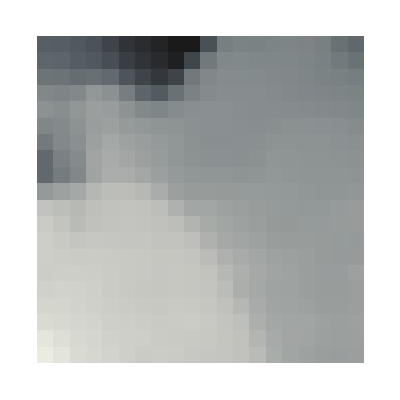
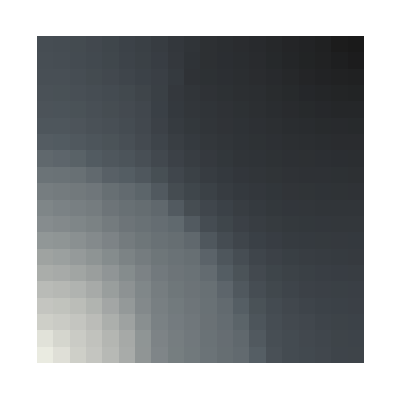
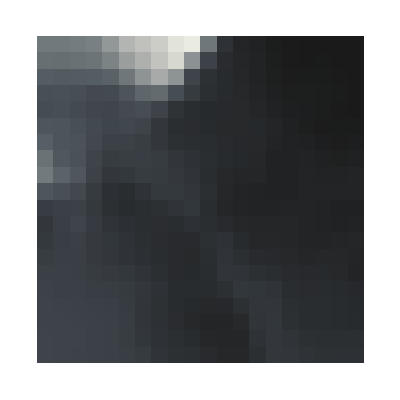
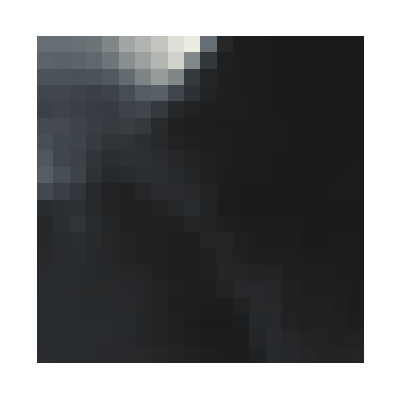

```mathematica
{{"\"AlpineColors\"", " — ", -Graphics-, "\"LakeColors\"", " — ", -Graphics-}, {"\"ArmyColors\"", " — ", -Graphics-, "\"MintColors\"", " — ", -Graphics-}, {"\"AtlanticColors\"", " — ", -Graphics-, "\"NeonColors\"", " — ", -Graphics-}, {"\"AuroraColors\"", " — ", -Graphics-, "\"PearlColors\"", " — ", -Graphics-}, {"\"AvocadoColors\"", " — ", -Graphics-, "\"PlumColors\"", " — ", -Graphics-}, {"\"BeachColors\"", " — ", -Graphics-, "\"RoseColors\"", " — ", -Graphics-}, {"\"CandyColors\"", " — ", -Graphics-, "\"SolarColors\"", " — ", -Graphics-}, {"\"CMYKColors\"", " — ", -Graphics-, "\"SouthwestColors\"", " — ", -Graphics-}, {"\"DeepSeaColors\"", " — ", -Graphics-, "\"StarryNightColors\"", " — ", -Graphics-}, {"\"FallColors\"", " — ", -Graphics-, "\"SunsetColors\"", " — ", -Graphics-}, {"\"FruitPunchColors\"", " — ", -Graphics-, "\"ThermometerColors\"", " — ", -Graphics-}, {"\"IslandColors\"", " — ", -Graphics-, "\"WatermelonColors\"", " — ", -Graphics-}, {, , , , , }, {"\"BrassTones\"", " — ", -Graphics-, "\"GreenPinkTones\"", " — ", -Graphics-}, {"\"BrownCyanTones\"", " — ", -Graphics-, "\"PigeonTones\"", " — ", -Graphics-}, {"\"CherryTones\"", " — ", -Graphics-, "\"RedBlueTones\"", " — ", -Graphics-}, {"\"CoffeeTones\"", " — ", -Graphics-, "\"RustTones\"", " — ", -Graphics-}, {"\"FuchsiaTones\"", " — ", -Graphics-, "\"SiennaTones\"", " — ", -Graphics-}, {"\"GrayTones\"", " — ", -Graphics-, "\"ValentineTones\"", " — ", -Graphics-}, {"\"GrayYellowTones\"", " — ", -Graphics-, , , }, {, , , , , }, {"\"DarkTerrain\"", " — ", -Graphics-, "\"LightTerrain\"", " — ", -Graphics-}, {"\"GreenBrownTerrain\"", " — ", -Graphics-, "\"SandyTerrain\"", " — ", -Graphics-}, {, , , , , }, {"\"BrightBands\"", " — ", -Graphics-, "\"DarkBands\"", " — ", -Graphics-}, {, , , , , }, {"\"Aquamarine\"", " — ", -Graphics-, "\"Pastel\"", " — ", -Graphics-}, {"\"BlueGreenYellow\"", " — ", -Graphics-, "\"Rainbow\"", " — ", -Graphics-}, {"\"DarkRainbow\"", " — ", -Graphics-, "\"TemperatureMap\"", " — ", -Graphics-}, {"\"LightTemperatureMap\"", " — ", -Graphics-, , , }}//Grid
{{"\"AlpineColors\"", " — ", -Graphics-, "\"LakeColors\"", " — ", -Graphics-}, {"\"ArmyColors\"", " — ", -Graphics-, "\"MintColors\"", " — ", -Graphics-}, {"\"AtlanticColors\"", " — ", -Graphics-, "\"NeonColors\"", " — ", -Graphics-}, {"\"AuroraColors\"", " — ", -Graphics-, "\"PearlColors\"", " — ", -Graphics-}, {"\"AvocadoColors\"", " — ", -Graphics-, "\"PlumColors\"", " — ", -Graphics-}, {"\"BeachColors\"", " — ", -Graphics-, "\"RoseColors\"", " — ", -Graphics-}, {"\"CandyColors\"", " — ", -Graphics-, "\"SolarColors\"", " — ", -Graphics-}, {"\"CMYKColors\"", " — ", -Graphics-, "\"SouthwestColors\"", " — ", -Graphics-}, {"\"DeepSeaColors\"", " — ", -Graphics-, "\"StarryNightColors\"", " — ", -Graphics-}, {"\"FallColors\"", " — ", -Graphics-, "\"SunsetColors\"", " — ", -Graphics-}, {"\"FruitPunchColors\"", " — ", -Graphics-, "\"ThermometerColors\"", " — ", -Graphics-}, {"\"IslandColors\"", " — ", -Graphics-, "\"WatermelonColors\"", " — ", -Graphics-}, {, , , , , }, {"\"BrassTones\"", " — ", -Graphics-, "\"GreenPinkTones\"", " — ", -Graphics-}, {"\"BrownCyanTones\"", " — ", -Graphics-, "\"PigeonTones\"", " — ", -Graphics-}, {"\"CherryTones\"", " — ", -Graphics-, "\"RedBlueTones\"", " — ", -Graphics-}, {"\"CoffeeTones\"", " — ", -Graphics-, "\"RustTones\"", " — ", -Graphics-}, {"\"FuchsiaTones\"", " — ", -Graphics-, "\"SiennaTones\"", " — ", -Graphics-}, {"\"GrayTones\"", " — ", -Graphics-, "\"ValentineTones\"", " — ", -Graphics-}, {"\"GrayYellowTones\"", " — ", -Graphics-, , , }, {, , , , , }, {"\"DarkTerrain\"", " — ", -Graphics-, "\"LightTerrain\"", " — ", -Graphics-}, {"\"GreenBrownTerrain\"", " — ", -Graphics-, "\"SandyTerrain\"", " — ", -Graphics-}, {, , , , , }, {"\"BrightBands\"", " — ", -Graphics-, "\"DarkBands\"", " — ", -Graphics-}, {, , , , , }, {"\"Aquamarine\"", " — ", -Graphics-, "\"Pastel\"", " — ", -Graphics-}, {"\"BlueGreenYellow\"", " — ", -Graphics-, "\"Rainbow\"", " — ", -Graphics-}, {"\"DarkRainbow\"", " — ", -Graphics-, "\"TemperatureMap\"", " — ", -Graphics-}, {"\"LightTemperatureMap\"", " — ", -Graphics-, , , }}
colorScheme="DarkRainbow";
somRenderWeights=RenderSOM[som,"Weights","ColorScheme"->colorScheme]
Row@IDslices@id1
```

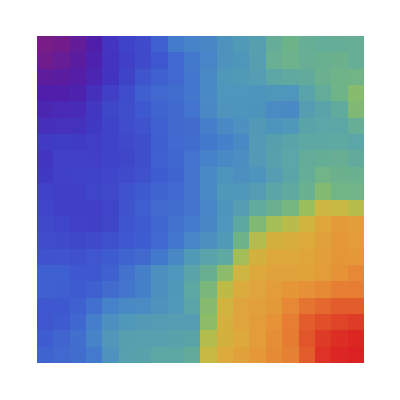
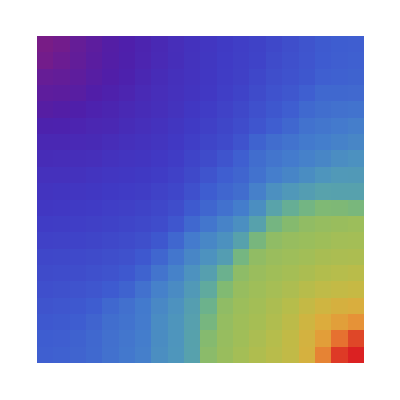
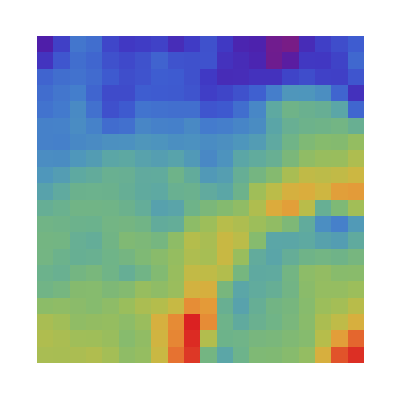
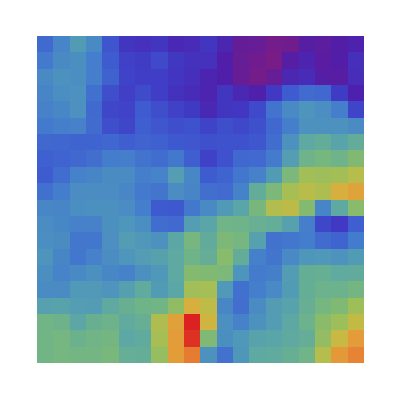

```mathematica
gradient="Rainbow";
IDslices[id1,gradient]
```

Finding the BMUs from the SOM

```mathematica
bmus = MapIndexed[First@#2->IDask[id1, {#1}][[1]]&, vecListFilter];
```

Run 1 time,  this line save to import and save clean subset

```mathematica
Export[NotebookDirectory[]<>"bmus_"<>user<>".m",bmus];
Export[NotebookDirectory[]<>"id1_"<>user<>".m",id1];
```

#### Run from here to load the trained SOM

```mathematica
id1_all_coords20x20_4
```

```mathematica
bmus=Import[NotebookDirectory[]<>"bmus_"<>user<>".m"];
id1=Import[NotebookDirectory[]<>"id1_"<>user<>".m"];
```

#### Rendering the SOM and start the send filter by form

This process takes around 3 to 4 minutes

```mathematica
som=GetSom[bmus,id1,vecListFilter,gradient];
indexListSorted=som["indexListSorted"];
som["somImg"]
```

-Graphics-

#### Export the image of the SOM

This process takes around 6 to 8 minutes

```mathematica
renderSom=RenderSom[som,eventListFilter,forceFilter,edgesConnection];
```

```mathematica
img=Image[Rasterize[renderSom["som"]]];
Export[NotebookDirectory[]<>"som"<>ToString@x<>ToString@x<>"_"<>user<>"_SOM.pdf",img];
```

```mathematica
somGrid=renderSom["som"];
```

```mathematica
white1=If[0.0001≤ Abs@#≥ 0,#,a]&/@#&/@subset["force"];
blueRed1=If[#<0,Blue,Red,White]&/@#&/@white1;

blueRedOri=If[#<0,Blue,Red]&/@#&/@subset["force"];
```

```mathematica
quant=Length[#]&/@indexListSorted;
Image[Rasterize[Grid[Partition[Thread[Range[id1[[1,4]]]->quant],x],Spacings->{0.5, 2},Frame->All]]]
```

-Graphics-

```mathematica
forceSorted=subset["force"][[#]]&/@indexListSorted;
coordsSorted=subset["points"][[#]]&/@indexListSorted;
```

Check sell number 1

```mathematica
number=1;
cells=Table[Graphics3D[
{Thickness[Abs[subset["force"]][[indexListSorted[[number,i]],#]]/700],
blueRed1[[indexListSorted[[number,i]],#]],Line[Partition[subset["points"][[indexListSorted[[number,i]]]],3][[edgesConnection[[#]]]]]
}&/@Range@Length@edgesConnection,Boxed->False(*,ViewPoint->Top*)],{i,1,12}];

Grid[Partition[cells,4]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"indexListSortedRe_"<>user<>".m",indexListSorted];
Export[NotebookDirectory[]<>"cell_quatityRe_"<>user<>".m",quant];
Export[NotebookDirectory[]<>"coordsSortedRe_"<>user<>".m",coordsSorted];
Export[NotebookDirectory[]<>"blueRed1_"<>user<>".m",blueRed1];
```